Model of immune-mediated feedbacks:

```mathematica
dp2=(1-p) p α-p t μ;
dt2=(γ+t (t-δ+p σ-t^2 χ))/δ;
```

Calculate the separatrix:

```mathematica
params={σ->0.2,δ->1,χ->0.2,α->1,μ->0.4,γ->0.15};sol=Table[{p0,Table[t0,{t0,0.5,1.1,0.001}][[Min[Flatten[Position[Table[{0.01,(p[50]/.NDSolve[{p'[T]==(dp2/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt2/.{p->p[T],t->t[T]}/.params),
p[0]==p0,t[0]==t0},{p,t},{T,0,50}])[[1]]},{t0,0.5,1.1,0.001}][[;;,2]],_?(#<0.01&)]]]]]},{p0,0.01,1.51,0.01}];
```

$Aborted

```mathematica
sol={{0.01,1.085},{0.02,1.0670000000000002},{0.03,1.053},{0.04,1.041},{0.05,1.03},{0.060000000000000005,1.021},{0.06999999999999999,1.012},{0.08,1.004},{0.09,0.996},{0.09999999999999999,0.989},{0.11,0.982},{0.12,0.976},{0.13,0.97},{0.14,0.964},{0.15000000000000002,0.9590000000000001},{0.16,0.9530000000000001},{0.17,0.948},{0.18000000000000002,0.944},{0.19,0.9390000000000001},{0.2,0.935},{0.21000000000000002,0.9299999999999999},{0.22,0.9259999999999999},{0.23,0.9219999999999999},{0.24000000000000002,0.9179999999999999},{0.25,0.915},{0.26,0.911},{0.27,0.907},{0.28,0.904},{0.29000000000000004,0.901},{0.3,0.897},{0.31,0.894},{0.32,0.891},{0.33,0.888},{0.34,0.885},{0.35000000000000003,0.882},{0.36000000000000004,0.879},{0.37,0.877},{0.38,0.874},{0.39,0.871},{0.4,0.869},{0.41000000000000003,0.866},{0.42000000000000004,0.864},{0.43,0.861},{0.44,0.859},{0.45,0.856},{0.46,0.854},{0.47000000000000003,0.852},{0.48000000000000004,0.8500000000000001},{0.49,0.847},{0.5,0.845},{0.51,0.843},{0.52,0.841},{0.53,0.839},{0.54,0.837},{0.55,0.835},{0.56,0.833},{0.5700000000000001,0.831},{0.5800000000000001,0.829},{0.59,0.8280000000000001},{0.6,0.8260000000000001},{0.61,0.8240000000000001},{0.62,0.8220000000000001},{0.63,0.8200000000000001},{0.64,0.819},{0.65,0.817},{0.66,0.815},{0.67,0.8140000000000001},{0.68,0.812},{0.6900000000000001,0.81},{0.7000000000000001,0.8089999999999999},{0.7100000000000001,0.8069999999999999},{0.72,0.806},{0.73,0.804},{0.74,0.8029999999999999},{0.75,0.8009999999999999},{0.76,0.8},{0.77,0.798},{0.78,0.7969999999999999},{0.79,0.7949999999999999},{0.8,0.794},{0.81,0.7929999999999999},{0.8200000000000001,0.7909999999999999},{0.8300000000000001,0.79},{0.8400000000000001,0.788},{0.85,0.787},{0.86,0.786},{0.87,0.784},{0.88,0.783},{0.89,0.782},{0.9,0.781},{0.91,0.779},{0.92,0.778},{0.93,0.777},{0.9400000000000001,0.776},{0.9500000000000001,0.775},{0.9600000000000001,0.773},{0.97,0.772},{0.98,0.771},{0.99,0.77},{1.,0.769},{1.01,0.768},{1.02,0.766},{1.03,0.765},{1.04,0.764},{1.05,0.763},{1.06,0.762},{1.07,0.761},{1.08,0.76},{1.09,0.759},{1.1,0.758},{1.11,0.757},{1.12,0.756},{1.1300000000000001,0.755},{1.1400000000000001,0.754},{1.1500000000000001,0.753},{1.1600000000000001,0.752},{1.17,0.751},{1.18,0.75},{1.19,0.749},{1.2,0.748},{1.21,0.747},{1.22,0.746},{1.23,0.745},{1.24,0.744},{1.25,0.743},{1.26,0.742},{1.27,0.741},{1.28,0.741},{1.29,0.74},{1.3,0.739},{1.31,0.738},{1.32,0.737},{1.33,0.736},{1.34,0.735},{1.35,0.734},{1.36,0.734},{1.37,0.733},{1.3800000000000001,0.732},{1.3900000000000001,0.731},{1.4000000000000001,0.73},{1.4100000000000001,0.729},{1.42,0.729},{1.43,0.728},{1.44,0.727},{1.45,0.726},{1.46,0.725},{1.47,0.725},{1.48,0.724},{1.49,0.723},{1.5,0.722},{1.51,0.722}};
```

Plot the isoclines, separatrix, and some trajectories in phase space:

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p→0.,t→0.181875},{p→0.89525,t→0.261876},{p→0.675092,t→0.812271},{p→0.,t→1.11296},{p→-0.410341,t→3.52585},{p→0.,t→3.70516}}

Power::infy: Infinite expression 1/0. encountered.

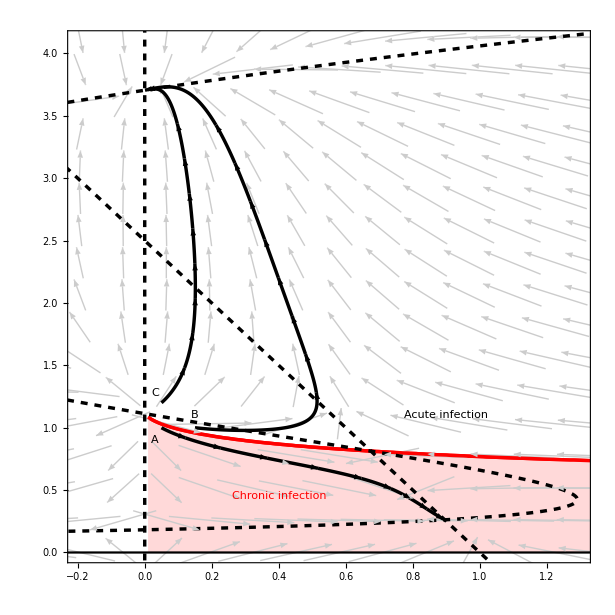

```mathematica
pisocline=Solve[dp2==0,p][[2,1,2]];
tisocline=Solve[dt2==0,p][[1,1,2]];
params={σ->0.2,δ->1,χ->0.2,α->1,μ->0.4,γ->0.15};
sol1=NDSolve[{p'[T]==(dp2/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt2/.{p->p[T],t->t[T]}/.params),
p[0]==0.15,t[0]==1},{p,t},{T,0,50}];
sol2=NDSolve[{p'[T]==(dp2/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt2/.{p->p[T],t->t[T]}/.params),
p[0]==0.05,t[0]==1},{p,t},{T,0,50}];
sol3=NDSolve[{p'[T]==(dp2/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt2/.{p->p[T],t->t[T]}/.params),
p[0]==0.05,t[0]==1.2},{p,t},{T,0,50}];
equil=Solve[{dp2==0,dt2==0}/.params, {p,t}]
Show[VectorPlot[{dp2/.params,dt2/.params},{p,-2,2},{t,0,8},VectorScale->{0.028,0.6,None},VectorStyle->{GrayLevel[1]},VectorPoints->32],
ListLinePlot[sol, PlotStyle->{Thickness[0.004], Red}, Filling->Bottom,FillingStyle->LightRed],
Plot[0.722, {x,0.01,1.5}, PlotStyle->{LightRed},Filling->Bottom,FillingStyle->LightRed],
VectorPlot[{dp2/.params,dt2/.params},{p,-2,2},{t,0,8},VectorScale->{0.028,0.6,None},VectorStyle->{GrayLevel[0.8]},VectorPoints->32],
ListLinePlot[sol, PlotStyle->{Thickness[0.004], Red}],ListLinePlot[Table[{tisocline/.params,t},{t,0,20,0.01}],PlotStyle->{Thickness[0.004],Dashed,Black},PlotRange->All],
ListLinePlot[Table[{pisocline/.params,t},{t,-2,15,0.01}],PlotStyle->{Thickness[0.004],Dashed,Black}],
ListLinePlot[Table[{0,t},{t,-1,12,0.01}],PlotStyle->{Thickness[0.004],Dashed,Black}],
ListLinePlot[Table[{p,0},{p,-2,8,0.01}],PlotStyle->{Black}],
ListLinePlot[Table[{(p[T]/.sol1)[[1]],(t[T]/.sol1)[[1]]},{T,0,20,0.01}],PlotStyle->{Thickness[0.004],Black},MeshFunctions->{#2&},Mesh->8,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.03]}]/.Line->Arrow,
ListLinePlot[Table[{(p[T]/.sol2)[[1]],(t[T]/.sol2)[[1]]},{T,0,20,0.01}],PlotStyle->{Thickness[0.004],Black},MeshFunctions->{#2&},Mesh->8,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.03]}]/.Line->Arrow,
ListLinePlot[Table[{(p[T]/.sol3)[[1]],(t[T]/.sol3)[[1]]},{T,0,10,0.01}],PlotStyle->{Thickness[0.004],Black},MeshFunctions->{#2&},Mesh->8,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.03]}]/.Line->Arrow,
Graphics[Text[Style[A,Large],{0.03,0.9}]],
Graphics[Text[Style[B,Large],{0.15,1.1}]],
Graphics[Text[Style[C,Large],{0.03,1.28}]],
Graphics[Text[Style[Acute infection,{Large,Black}],{0.9,1.1}]],
Graphics[Text[Style[Chronic infection,{Large,Red}],{0.4,0.45}]],
PlotRange->{{-0.2,1.3},{0,4.1}}]
```

Parasite-mediated feedback model:

```mathematica
dt=γ+β p-ν t-α p/(1+p) t;
dp=λ p (1-p)-κ p t;
```

Separatrix for this model:

```mathematica
params={β->2,γ->1,κ->0.8,λ->4,α->3,ν->0.0001};
soln=Table[{p0,
Table[t0,{t0,Table[t0,{t0,1,10,0.1}][[Min[Flatten[Position[Table[(p[50]/.NDSolve[{p'[T]==(dp/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt/.{p->p[T],t->t[T]}/.params),
p[0]==p0,t[0]==t0},{p,t},{T,0,50}])[[1]],{t0,1,10,0.1}],_?(#<0.01&)]]]-1]],
Table[t0,{t0,1,10,0.1}][[Min[Flatten[Position[Table[(p[50]/.NDSolve[{p'[T]==(dp/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt/.{p->p[T],t->t[T]}/.params),
p[0]==p0,t[0]==t0},{p,t},{T,0,50}])[[1]],{t0,1,10,0.1}],_?(#<0.01&)]]]]],0.001}][[Min[Flatten[Position[Table[(p[50]/.NDSolve[{p'[T]==(dp/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt/.{p->p[T],t->t[T]}/.params),
p[0]==p0,t[0]==t0},{p,t},{T,0,50}])[[1]],{t0,Table[t0,{t0,1,10,0.1}][[Min[Flatten[Position[Table[(p[50]/.NDSolve[{p'[T]==(dp/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt/.{p->p[T],t->t[T]}/.params),
p[0]==p0,t[0]==t0},{p,t},{T,0,50}])[[1]],{t0,1,10,0.1}],_?(#<0.01&)]]]-1]],
Table[t0,{t0,1,10,0.1}][[Min[Flatten[Position[Table[(p[50]/.NDSolve[{p'[T]==(dp/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt/.{p->p[T],t->t[T]}/.params),
p[0]==p0,t[0]==t0},{p,t},{T,0,50}])[[1]],{t0,1,10,0.1}],_?(#<0.01&)]]]]],0.001}],_?(#<0.01&)]]]]]},{p0,0.001,1.501,0.01}]
```

{{0.001,1.788},{0.011,2.9},{0.021,3.293},{0.031,3.561},{0.041,3.77},{0.051,3.944},{0.061,4.095},{0.071,4.229},{0.081,4.35},{0.091,4.461},{0.101,4.563},{0.111,4.659},{0.121,4.748},{0.131,4.832},{0.141,4.912},{0.151,4.988},{0.161,5.06},{0.171,5.129},{0.181,5.194},{0.191,5.258},{0.201,5.318},{0.211,5.377},{0.221,5.433},{0.231,5.488},{0.241,5.541},{0.251,5.592},{0.261,5.641},{0.271,5.689},{0.281,5.736},{0.291,5.781},{0.301,5.825},{0.311,5.868},{0.321,5.91},{0.331,5.951},{0.341,5.991},{0.351,6.03},{0.361,6.067},{0.371,6.105},{0.381,6.141},{0.391,6.176},{0.401,6.211},{0.411,6.245},{0.421,6.278},{0.431,6.31},{0.441,6.342},{0.451,6.373},{0.461,6.404},{0.471,6.434},{0.481,6.463},{0.491,6.492},{0.501,6.52},{0.511,6.548},{0.521,6.575},{0.531,6.602},{0.541,6.629},{0.551,6.655},{0.561,6.68},{0.571,6.705},{0.581,6.73},{0.591,6.754},{0.601,6.778},{0.611,6.801},{0.621,6.824},{0.631,6.847},{0.641,6.869},{0.651,6.891},{0.661,6.913},{0.671,6.934},{0.681,6.955},{0.691,6.976},{0.701,6.996},{0.711,7.016},{0.721,7.036},{0.731,7.056},{0.741,7.075},{0.751,7.094},{0.761,7.113},{0.771,7.131},{0.781,7.149},{0.791,7.167},{0.801,7.185},{0.811,7.203},{0.821,7.22},{0.831,7.237},{0.841,7.254},{0.851,7.27},{0.861,7.287},{0.871,7.303},{0.881,7.319},{0.891,7.335},{0.901,7.35},{0.911,7.366},{0.921,7.381},{0.931,7.396},{0.941,7.411},{0.951,7.425},{0.961,7.44},{0.971,7.454},{0.981,7.468},{0.991,7.482},{1.001,7.496},{1.011,7.51},{1.021,7.523},{1.031,7.536},{1.041,7.55},{1.051,7.563},{1.061,7.576},{1.071,7.588},{1.081,7.601},{1.091,7.613},{1.101,7.626},{1.111,7.638},{1.121,7.65},{1.131,7.662},{1.141,7.674},{1.151,7.686},{1.161,7.697},{1.171,7.709},{1.181,7.72},{1.191,7.731},{1.201,7.742},{1.211,7.753},{1.221,7.764},{1.231,7.775},{1.241,7.785},{1.251,7.796},{1.261,7.806},{1.271,7.817},{1.281,7.827},{1.291,7.837},{1.301,7.847},{1.311,7.857},{1.321,7.867},{1.331,7.877},{1.341,7.886},{1.351,7.896},{1.361,7.905},{1.371,7.915},{1.381,7.924},{1.391,7.933},{1.401,7.942},{1.411,7.951},{1.421,7.96},{1.431,7.969},{1.441,7.978},{1.451,7.986},{1.461,7.995},{1.471,8.004},{1.481,8.012},{1.491,8.02},{1.501,8.029}}

```mathematica
Table[(p[50]/.NDSolve[{p'[T]==(dp/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt/.{p->p[T],t->t[T]}/.params),
p[0]==0.0001,t[0]==t0},{p,t},{T,0,50}])[[1]],{t0,0.99,1,0.001}]
```

{0.609383,0.609383,5.73611×10^-11,1.59554×10^-11,4.29608×10^-11,7.97574×10^-9,-7.75783×10^-12,3.29211×10^-12,-1.88071×10^-11,4.27875×10^-9,-5.85899×10^-10}

```mathematica
Table[(p[50]/.NDSolve[{p'[T]==(dp/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt/.{p->p[T],t->t[T]}/.params),
p[0]==0.000003,t[0]==t0},{p,t},{T,0,50}])[[1]],{t0,0.01,0.02,0.001}]
```

{0.609383,0.609383,0.609383,0.609383,0.609383,0.609383,0.609383,0.609383,-2.93395×10^-11,1.44282×10^-10,-1.29376×10^-9}

```mathematica
soln=Join[{{0.000003,0.018},{0.00001,0.329},{0.0001,0.993}},soln]
```

{{3.×10^-6,0.018},{0.00001,0.329},{0.0001,0.993},{0.001,1.788},{0.011,2.9},{0.021,3.293},{0.031,3.561},{0.041,3.77},{0.051,3.944},{0.061,4.095},{0.071,4.229},{0.081,4.35},{0.091,4.461},{0.101,4.563},{0.111,4.659},{0.121,4.748},{0.131,4.832},{0.141,4.912},{0.151,4.988},{0.161,5.06},{0.171,5.129},{0.181,5.194},{0.191,5.258},{0.201,5.318},{0.211,5.377},{0.221,5.433},{0.231,5.488},{0.241,5.541},{0.251,5.592},{0.261,5.641},{0.271,5.689},{0.281,5.736},{0.291,5.781},{0.301,5.825},{0.311,5.868},{0.321,5.91},{0.331,5.951},{0.341,5.991},{0.351,6.03},{0.361,6.067},{0.371,6.105},{0.381,6.141},{0.391,6.176},{0.401,6.211},{0.411,6.245},{0.421,6.278},{0.431,6.31},{0.441,6.342},{0.451,6.373},{0.461,6.404},{0.471,6.434},{0.481,6.463},{0.491,6.492},{0.501,6.52},{0.511,6.548},{0.521,6.575},{0.531,6.602},{0.541,6.629},{0.551,6.655},{0.561,6.68},{0.571,6.705},{0.581,6.73},{0.591,6.754},{0.601,6.778},{0.611,6.801},{0.621,6.824},{0.631,6.847},{0.641,6.869},{0.651,6.891},{0.661,6.913},{0.671,6.934},{0.681,6.955},{0.691,6.976},{0.701,6.996},{0.711,7.016},{0.721,7.036},{0.731,7.056},{0.741,7.075},{0.751,7.094},{0.761,7.113},{0.771,7.131},{0.781,7.149},{0.791,7.167},{0.801,7.185},{0.811,7.203},{0.821,7.22},{0.831,7.237},{0.841,7.254},{0.851,7.27},{0.861,7.287},{0.871,7.303},{0.881,7.319},{0.891,7.335},{0.901,7.35},{0.911,7.366},{0.921,7.381},{0.931,7.396},{0.941,7.411},{0.951,7.425},{0.961,7.44},{0.971,7.454},{0.981,7.468},{0.991,7.482},{1.001,7.496},{1.011,7.51},{1.021,7.523},{1.031,7.536},{1.041,7.55},{1.051,7.563},{1.061,7.576},{1.071,7.588},{1.081,7.601},{1.091,7.613},{1.101,7.626},{1.111,7.638},{1.121,7.65},{1.131,7.662},{1.141,7.674},{1.151,7.686},{1.161,7.697},{1.171,7.709},{1.181,7.72},{1.191,7.731},{1.201,7.742},{1.211,7.753},{1.221,7.764},{1.231,7.775},{1.241,7.785},{1.251,7.796},{1.261,7.806},{1.271,7.817},{1.281,7.827},{1.291,7.837},{1.301,7.847},{1.311,7.857},{1.321,7.867},{1.331,7.877},{1.341,7.886},{1.351,7.896},{1.361,7.905},{1.371,7.915},{1.381,7.924},{1.391,7.933},{1.401,7.942},{1.411,7.951},{1.421,7.96},{1.431,7.969},{1.441,7.978},{1.451,7.986},{1.461,7.995},{1.471,8.004},{1.481,8.012},{1.491,8.02},{1.501,8.029}}

Isoclines, separatrix, and example trajectories:

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p→0.,t→10000.},{p→0.0964785,t→4.51761},{p→0.609383,t→1.95308}}

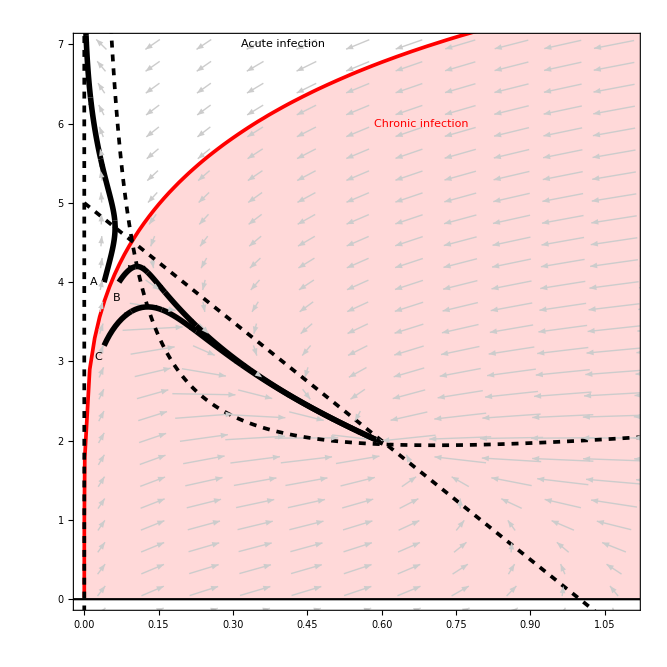

```mathematica
tisocline=Solve[dt==0,t][[1,1,2]]//Simplify;
pisocline=Solve[dp==0,t][[1,1,2]];
params={β->2,γ->1,κ->0.8,λ->4,α->3,ν->0.0001};
equil=Solve[{dp==0,dt==0}/.params,{p,t}]

sol1=NDSolve[{p'[T]==(dp/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt/.{p->p[T],t->t[T]}/.params),
p[0]==0.04,t[0]==4},{p,t},{T,0,50}];
sol2=NDSolve[{p'[T]==(dp/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt/.{p->p[T],t->t[T]}/.params),
p[0]==0.07,t[0]==4},{p,t},{T,0,50}];
sol3=NDSolve[{p'[T]==(dp/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt/.{p->p[T],t->t[T]}/.params),
p[0]==0.04,t[0]==3.2},{p,t},{T,0,50}];
Show[VectorPlot[{dp/.params,dt/.params},{p,-1,2},{t,-1,7},VectorScale->{0.015,0.5,None},VectorStyle->{GrayLevel[1]},VectorPoints->30],
ListLinePlot[soln, PlotStyle->{Thickness[0.004], Red}, Filling->Bottom,FillingStyle->LightRed],
VectorPlot[{dp/.params,dt/.params},{p,-1,2},{t,-1,7},VectorScale->{0.015,0.5,None},VectorStyle->{GrayLevel[0.8]},VectorPoints->30],
ListLinePlot[Table[{p,tisocline/.params},{p,0,5,0.001}],PlotStyle->{Thickness[0.004],Dashed,Black},PlotRange->All],
ListLinePlot[Table[{p, pisocline/.params},{p,0,5,0.01}],PlotStyle->{Thickness[0.004],Dashed,Black}],
ListLinePlot[Table[{0,t},{t,-1,12,0.01}],PlotStyle->{Thickness[0.004],Dashed,Black}],
ListLinePlot[Table[{p,0},{p,-1,8,0.01}],PlotStyle->{Medium,Black}],
ListLinePlot[Table[{(p[T]/.sol1)[[1]],(t[T]/.sol1)[[1]]},{T,0,10,0.01}],PlotStyle->{Thickness[0.006],Black},MeshFunctions->{#2&},Mesh->8,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.03]}]/.Line->Arrow,
ListLinePlot[Table[{(p[T]/.sol2)[[1]],(t[T]/.sol2)[[1]]},{T,0,10,0.1}],PlotStyle->{Thickness[0.006],Black},MeshFunctions->{#3&},Mesh->8,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.03]}]/.Line->Arrow,
ListLinePlot[Table[{(p[T]/.sol3)[[1]],(t[T]/.sol3)[[1]]},{T,0,8,0.1}],PlotStyle->{Thickness[0.006],Black},MeshFunctions->{#3&},Mesh->8,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.03]}]/.Line->Arrow,
Graphics[Text[Style[A,Large],{0.02,4}]],
Graphics[Text[Style[B,Large],{0.065,3.8}]],
Graphics[Text[Style[C,Large],{0.028,3.05}]],
Graphics[Text[Style[Acute infection,{Large,Black}],{0.4,7}]],
Graphics[Text[Style[Chronic infection,{Large,Red}],{0.68,6}]],
PlotRange->{{0,1.1},{0,7}}]
```

### Immune-mediated feedback model: simulation and analysis

#### Simulation study

Here is the cytokine-T cell model based on Yates et al. 2000.

```mathematica
dp=α p(1-p)-μ p t
ds=t-δ s
dt=σ p s+s t-χ s t^2-t
```

(1-p) p α-p t μ

t-s δ

-t+s t+p s σ-s t^2 χ

```mathematica
params={σ->0.2,δ->0.3,χ->0.1,α->0.5,μ->0.3}
equil=Solve[{dp==0,ds==0,dt==0}/.params,{p,s,t}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p→0.,s→0.,t→0.},{p→1.,s→0.,t→0.},{p→0.930914,s→0.38381,t→0.115143},{p→0.,s→1.03195,t→0.309584},{p→-4.21091,s→28.9495,t→8.68486},{p→0.,s→32.3014,t→9.69042}}

Bistability!

```mathematica
Eigenvalues[D[{dp,ds,dt},{{p,s,t}}]/.params/.equil[[2]]]
Eigenvalues[D[{dp,ds,dt},{{p,s,t}}]/.params/.equil[[6]]]
```

{-1.21789,-0.5,-0.0821092}

{-31.3111,-2.40712,-0.290326}

Proof of bistability!

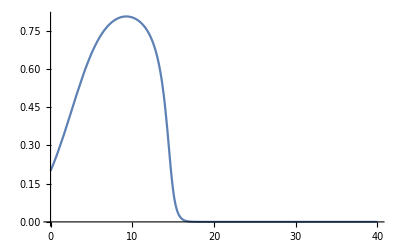

```mathematica
sol=NDSolve[{p'[T]==(dp/.{p->p[T],t->t[T],s->s[T]})/.params,
s'[T]==(ds/.{p->p[T],t->t[T],s->s[T]})/.params,
t'[T]==(dt/.{p->p[T],t->t[T],s->s[T]})/.params,
p[0]==0.2,s[0]==1,t[0]==0.1},{p,s,t},{T,0,40}];
Plot[p[T]/.sol,{T,0,40}]
```

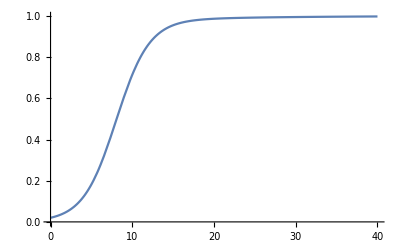

```mathematica
sol=NDSolve[{p'[T]==(dp/.{p->p[T],t->t[T],s->s[T]})/.params,
s'[T]==(ds/.{p->p[T],t->t[T],s->s[T]})/.params,
t'[T]==(dt/.{p->p[T],t->t[T],s->s[T]})/.params,
p[0]==0.02,s[0]==1,t[0]==0.1},{p,s,t},{T,0,40}];
Plot[p[T]/.sol,{T,0,40}]
```

Now, plot how bistability comes and goes as you vary a parameter - maybe σ?

With higher values of σ, the chronic infection equilibrium is unstable and the acute infection equilibrium is stable.

```mathematica
params={σ->0.4,δ->0.3,χ->0.1,α->0.5,μ->0.3};
equil=Solve[{dp==0,ds==0,dt==0}/.params,{p,s,t}]
Eigenvalues[D[{dp,ds,dt},{{p,s,t}}]/.params/.equil[[3]]]
Eigenvalues[D[{dp,ds,dt},{{p,s,t}}]/.params/.equil[[5]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p→1.07763,s→-0.431255,t→-0.129377},{p→0.,s→0.,t→0.},{p→1.,s→0.,t→0.},{p→0.,s→1.03195,t→0.309584},{p→-3.63763,s→25.7646,t→7.72938},{p→0.,s→32.3014,t→9.69042}}

{-1.37284,-0.5,0.0728416}

{-15.7248,2.46442,-0.285093}

Here’s where the chronic infection equilibrium loses its stability

```mathematica
params={σ->0.3,δ->0.3,χ->0.1,α->0.5,μ->0.3};
equil=Solve[{dp==0,ds==0,dt==0}/.params,{p,s,t}]
Eigenvalues[D[{dp,ds,dt},{{p,s,t}}]/.params/.equil[[2]]]
Eigenvalues[D[{dp,ds,dt},{{p,s,t}}]/.params/.equil[[5]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p→0.,s→0.,t→0.},{p→1.,s→0.,t→0.},{p→0.,s→1.03195,t→0.309584},{p→-3.92,s→27.3333,t→8.2},{p→0.,s→32.3014,t→9.69042}}

{-1.3,-0.5,0.}

{-31.3111,-2.40712,-0.290326}

```mathematica
params={σ->0.2,δ->0.3,χ->0.1,α->0.5,μ->0.3};
equil=Solve[{dp==0,ds==0,dt==0}/.params,{p,s,t}]
Eigenvalues[D[{dp,ds,dt},{{p,s,t}}]/.params/.equil[[2]]]
Eigenvalues[D[{dp,ds,dt},{{p,s,t}}]/.params/.equil[[6]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p→0.,s→0.,t→0.},{p→1.,s→0.,t→0.},{p→0.930914,s→0.38381,t→0.115143},{p→0.,s→1.03195,t→0.309584},{p→-4.21091,s→28.9495,t→8.68486},{p→0.,s→32.3014,t→9.69042}}

{-1.21789,-0.5,-0.0821092}

{-31.3111,-2.40712,-0.290326}

But bistability is not lost, even when σ goes to zero - the acute infection equilibrium is always stable.

```mathematica
params={σ->0,δ->0.3,χ->0.1,α->0.5,μ->0.3};
equil=Solve[{dp==0,ds==0,dt==0}/.params,{p,s,t}]
Eigenvalues[D[{dp,ds,dt},{{p,s,t}}]/.params/.equil[[2]]]
Eigenvalues[D[{dp,ds,dt},{{p,s,t}}]/.params/.equil[[6]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p→0.,s→0.,t→0.},{p→1.,s→-3.28955×10^-16,t→-8.88178×10^-17},{p→0.,s→1.03195,t→0.309584},{p→0.814249,s→1.03195,t→0.309584},{p→-4.81425,s→32.3014,t→9.69042},{p→0.,s→32.3014,t→9.69042}}

{-1.,-0.5,-0.3}

{-31.3111,-2.40712,-0.290326}

Here is how the unstable parasite equilibrium changes as you increase σ.

```mathematica
Table[Solve[{dp==0,ds==0,dt==0}/.{σ->Sval,δ->0.3,χ->0.1,α->0.5,μ->0.3},{p,s,t}][[3,1,2]],{Sval,0.01, 0.29,0.01}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{0.819486,0.82478,0.830133,0.835546,0.841018,0.846551,0.852147,0.857805,0.863526,0.869312,0.875163,0.881081,0.887065,0.893118,0.899239,0.905431,0.911693,0.918027,0.924434,0.930914,0.937469,0.9441,0.950808,0.957594,0.964458,0.971402,0.978428,0.985535,0.992725}

Here’s a picture of the bifurcation plot showing the stable and unstable equilibria.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

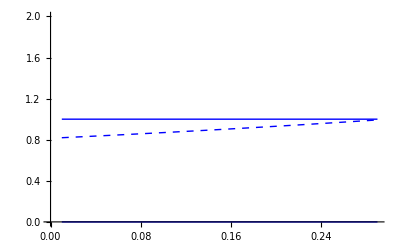

```mathematica
Show[ListLinePlot[Table[{Sval,Solve[{dp==0,ds==0,dt==0}/.{σ->Sval,δ->0.3,χ->0.1,α->0.5,μ->0.3},{p,s,t}][[2,1,2]]},{Sval,0.01, 0.29,0.01}],PlotStyle->{Thick,Blue}],ListLinePlot[Table[{Sval,Solve[{dp==0,ds==0,dt==0}/.{σ->Sval,δ->0.3,χ->0.1,α->0.5,μ->0.3},{p,s,t}][[3,1,2]]},{Sval,0.01, 0.29,0.01}],PlotStyle->{Thick,Dashed,Blue}],
ListLinePlot[Table[{Sval,Solve[{dp==0,ds==0,dt==0}/.{σ->Sval,δ->0.3,χ->0.1,α->0.5,μ->0.3},{p,s,t}][[6,1,2]]},{Sval,0.01, 0.29,0.01}],PlotStyle->{Thick,Blue}]]
```

Here’s how the unstable T cell response changes as you increase σ.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

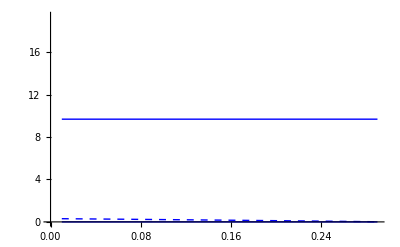

```mathematica
Show[ListLinePlot[Table[{Sval,Solve[{dp==0,ds==0,dt==0}/.{σ->Sval,δ->0.3,χ->0.1,α->0.5,μ->0.3},{p,s,t}][[6,3,2]]},{Sval,0.01, 0.29,0.01}],PlotStyle->{Thick,Blue}],ListLinePlot[Table[{Sval,Solve[{dp==0,ds==0,dt==0}/.{σ->Sval,δ->0.3,χ->0.1,α->0.5,μ->0.3},{p,s,t}][[3,3,2]]},{Sval,0.01, 0.29,0.01}],PlotStyle->{Thick,Dashed,Blue}],
ListLinePlot[Table[{Sval,Solve[{dp==0,ds==0,dt==0}/.{σ->Sval,δ->0.3,χ->0.1,α->0.5,μ->0.3},{p,s,t}][[2,3,2]]},{Sval,0.01, 0.29,0.01}],PlotStyle->{Thick,Blue}]]
```

And here’s how the unstable cytokine response changes as you increase σ.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

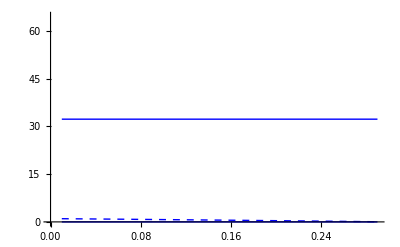

```mathematica
Show[ListLinePlot[Table[{Sval,Solve[{dp==0,ds==0,dt==0}/.{σ->Sval,δ->0.3,χ->0.1,α->0.5,μ->0.3},{p,s,t}][[6,2,2]]},{Sval,0.01, 0.29,0.01}],PlotStyle->{Thick,Blue}],ListLinePlot[Table[{Sval,Solve[{dp==0,ds==0,dt==0}/.{σ->Sval,δ->0.3,χ->0.1,α->0.5,μ->0.3},{p,s,t}][[3,2,2]]},{Sval,0.01, 0.29,0.01}],PlotStyle->{Thick,Dashed,Blue}],
ListLinePlot[Table[{Sval,Solve[{dp==0,ds==0,dt==0}/.{σ->Sval,δ->0.3,χ->0.1,α->0.5,μ->0.3},{p,s,t}][[2,2,2]]},{Sval,0.01, 0.29,0.01}],PlotStyle->{Thick,Blue}]]
```

#### Analysis: isoclines and analytical tractability

OKAY!! So, using this image, can we understand why a low dose leads to chronic whereas a high dose leads to clearance?

Here’s a thought: can I create a nice plot showing the stable and unstable equilibria, as in a L-V competition model?? That would be a beautiful way of showing it.

Maybe I can do it by a simplification, assuming a quasi-equilibrium for cytokines. Can that still produce bistability?

```mathematica
dp2=(1-p) p α-p t μ
(* dt2=Simplify[dt/.Solve[ds==0,s][[1]]] *)
dt2=(t (t-δ+p σ-t^2 χ))/δ
```

Yes it can!

```mathematica
params={σ->0.2,δ->0.3,χ->0.1,α->0.5,μ->0.3};
equil=Solve[{dp2==0,dt2==0}/.params,{p,t}]
(* chronic equilibrium is stable *)
Eigenvalues[D[{dp2,dt2},{{p,t}}]]/.params/.equil[[1]]
(* acute equilibrium is stable *)
Eigenvalues[D[{dp2,dt2},{{p,t}}]]/.params/.equil[[6]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p→1.,t→-9.86865×10^-17},{p→0.,t→0.},{p→0.930914,t→0.115143},{p→0.,t→0.309584},{p→-4.21091,t→8.68486},{p→0.,t→9.69042}}

{-0.5,-0.333333}

{-30.3014,-2.40712}

But if you increase σ, the chronic equilibrium becomes unstable! Just like before.

```mathematica
params={σ->0.4,δ->0.3,χ->0.1,α->0.5,μ->0.3};
equil=Solve[{dp2==0,dt2==0}/.params,{p,t}]
(* chronic equilibrium is stable *)
Eigenvalues[D[{dp2,dt2},{{p,t}}]]/.params/.equil[[1]]
(* acute equilibrium is stable *)
Eigenvalues[D[{dp2,dt2},{{p,t}}]]/.params/.equil[[6]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p→1.,t→-9.86865×10^-17},{p→1.07763,t→-0.129377},{p→0.,t→0.},{p→0.,t→0.309584},{p→-3.63763,t→7.72938},{p→0.,t→9.69042}}

{-0.5,0.333333}

{-30.3014,-2.40712}

So, let’s plot the isoclines for the bistability case.

```mathematica
pisocline=Solve[dp2==0,t][[1,1,2]]
tisocline=Solve[dt2==0,p][[1,1,2]]
```

-((-1+p) α)/μ

(-t+δ+t^2 χ)/σ

When does the t isocline intersect the p axis?

```mathematica
Solve[tisocline==0,t]
```

{{t→(1-√(1-4 δ χ))/(2 χ)},{t→(1+√(1-4 δ χ))/(2 χ)}}

Thus we know that the t isocline is a parabola as long as 1-4 δ χ > 0. If this is less than zero, then the t isocline is never equal to zero, implying that there is no equilibrium where the immune response is positive and the parasite is extinct. That case is biologically meaningless, so we don’t need to consider it any further.

When it is a parabola (and 1-4 δ χ > 0), which direction does the parabola point? I.e., at the peak of the parabola, is the p value positive or negative?

The peak of the t isocline is found at this value of t:

```mathematica
Solve[D[tisocline,t]==0,t]
```

{{t→1/(2 χ)}}

The p value at this point is

```mathematica
tisocline/.{t->1/(2 χ)}
```

(δ-1/(4 χ))/σ

Since we know that 1-4 δ χ > 0, we also know that δ < 1/(4 χ), so the p value is negative. Thus, the t isocline will always be a parabola facing to the left.

now the key question is: what happens to these isoclines as you change the strength of the feedbacks?

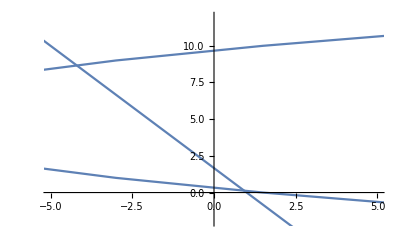

```mathematica
params={σ->0.2,δ->0.3,χ->0.1,α->0.5,μ->0.3};
Show[ListLinePlot[Table[{p,pisocline/.params},{p,-10,10}]],
ListLinePlot[Table[{tisocline/.params,t},{t,-2,12}]],PlotRange->{{-5,5},{-2,12}}]
```

Zooming in to look at the key range:

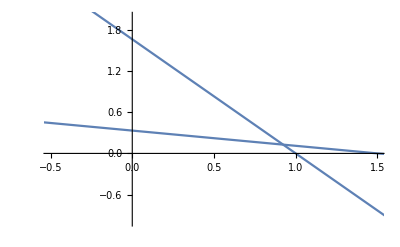

```mathematica
params={σ->0.2,δ->0.3,χ->0.1,α->0.5,μ->0.3};
Show[ListLinePlot[Table[{p,pisocline/.params},{p,-10,10}]],
ListLinePlot[Table[{tisocline/.params,t},{t,-2,12}]],PlotRange->{{-0.5,1.5},{-1,2}}]
```

You can see that, at the point where the chronic infection equilibrium becomes unstable, the two isoclines intersect at the chronic infection equilibrium.

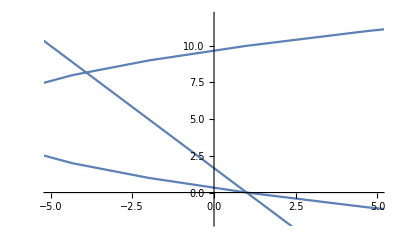

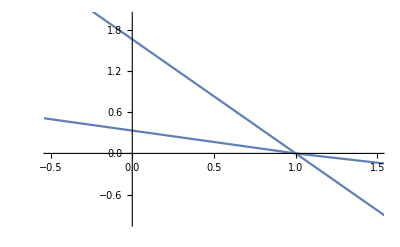

```mathematica
params={σ->0.3,δ->0.3,χ->0.1,α->0.5,μ->0.3};
Show[ListLinePlot[Table[{p,pisocline/.params},{p,-10,10}]],
ListLinePlot[Table[{tisocline/.params,t},{t,-2,12}]],PlotRange->{{-5,5},{-2,12}}]
Show[ListLinePlot[Table[{p,pisocline/.params},{p,-10,10}]],
ListLinePlot[Table[{tisocline/.params,t},{t,-2,12}]],PlotRange->{{-0.5,1.5},{-1,2}}]
```

Here, the internal equilibrium has disappeared and only the acute infection equilibrium is stable.

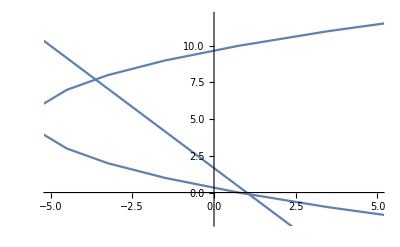

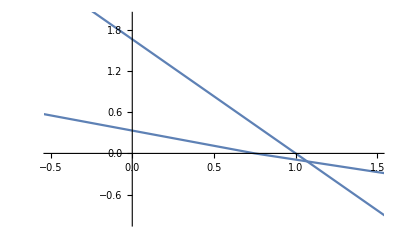

```mathematica
params={σ->0.4,δ->0.3,χ->0.1,α->0.5,μ->0.3};
Show[ListLinePlot[Table[{p,pisocline/.params},{p,-10,10}]],
ListLinePlot[Table[{tisocline/.params,t},{t,-2,12}]],PlotRange->{{-5,5},{-2,12}}]
Show[ListLinePlot[Table[{p,pisocline/.params},{p,-10,10}]],
ListLinePlot[Table[{tisocline/.params,t},{t,-2,12}]],PlotRange->{{-0.5,1.5},{-1,2}}]
```

In theory it should be possible to make the acute infection equilibrium unstable. This will happen when the intersection of the t isocline with the t axis is equal to the value of the p isocline when p = 0.
Specifically, if (1+√(1-4 δ χ))/(2 χ)==α/μ, the acute infection equilibrium should become unstable.

```mathematica
Solve[tisocline==0,t]
pisocline/.p->0
(1+√(1-4 δ χ))/(2 χ)==α/μ
```

{{t→(1-√(1-4 δ χ))/(2 χ)},{t→(1+√(1-4 δ χ))/(2 χ)}}

α/μ

```mathematica
params;
Solve[α/μ==((1+√(1-4 δ χ))/(2 χ)/.params),α]
```

{{α→9.69042 μ}}

Here is such a case:

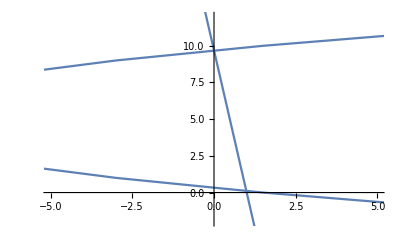

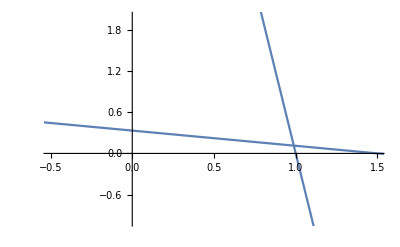

```mathematica
params={σ->0.2,δ->0.3,χ->0.1,α->9.69041575982343 0.3,μ->0.3};
Show[ListLinePlot[Table[{p,pisocline/.params},{p,-10,10}]],
ListLinePlot[Table[{tisocline/.params,t},{t,-2,12}]],PlotRange->{{-5,5},{-2,12}}]
Show[ListLinePlot[Table[{p,pisocline/.params},{p,-10,10}]],
ListLinePlot[Table[{tisocline/.params,t},{t,-2,12}]],PlotRange->{{-0.5,1.5},{-1,2}}]
```

And if you increase the value of α a bit further:

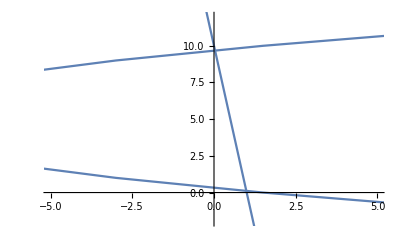

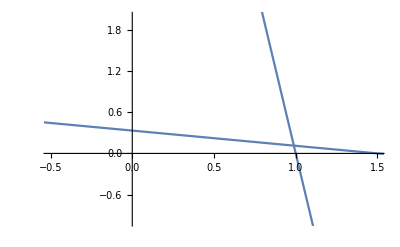

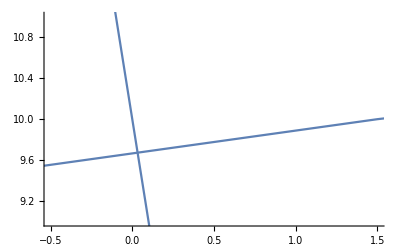

```mathematica
params={σ->0.2,δ->0.3,χ->0.1,α->3,μ->0.3};
Show[ListLinePlot[Table[{p,pisocline/.params},{p,-10,10}]],
ListLinePlot[Table[{tisocline/.params,t},{t,-2,12}]],PlotRange->{{-5,5},{-2,12}}]
Show[ListLinePlot[Table[{p,pisocline/.params},{p,-10,10}]],
ListLinePlot[Table[{tisocline/.params,t},{t,-2,12}]],PlotRange->{{-0.5,1.5},{-1,2}}]
Show[ListLinePlot[Table[{p,pisocline/.params},{p,-10,10}]],
ListLinePlot[Table[{tisocline/.params,t},{t,-2,12}]],PlotRange->{{-0.5,1.5},{9,11}}]
```

Okay, I’m starting to figure some shit out here. There are really two interacting pieces here, and you cannot disentangle them. Bistability/Allee effects don’t just apply to the parasite, they also apply to the immune system.

```mathematica
dp2=(1-p) p α-p t μ;
(* dt2=Simplify[dt/.Solve[ds==0,s][[1]]] *)
dt2=(γ+t (t-δ+p σ-t^2 χ))/δ;
```

```mathematica
pisocline=Solve[dp2==0,p][[2,1,2]]
tisocline=Solve[dt2==0,p][[1,1,2]]
```

(α-t μ)/α

(-t^2-γ+t δ+t^3 χ)/(t σ)

```mathematica
Solve[tisocline==0,t]
Solve[D[tisocline,t]==0,t]
Solve[pisocline==0,t]
```

{{t→1/(3 χ)-(2^(1/3) (-1+3 δ χ))/(3 χ (2-9 δ χ+27 γ χ^2+√(4 (-1+3 δ χ)^3+(2-9 δ χ+27 γ χ^2)^2))^(1/3))+((2-9 δ χ+27 γ χ^2+√(4 (-1+3 δ χ)^3+(2-9 δ χ+27 γ χ^2)^2))^(1/3))/(3 2^(1/3) χ)},{t→1/(3 χ)+((1+ⅈ √3) (-1+3 δ χ))/(3 2^(2/3) χ (2-9 δ χ+27 γ χ^2+√(4 (-1+3 δ χ)^3+(2-9 δ χ+27 γ χ^2)^2))^(1/3))-((1-ⅈ √3) (2-9 δ χ+27 γ χ^2+√(4 (-1+3 δ χ)^3+(2-9 δ χ+27 γ χ^2)^2))^(1/3))/(6 2^(1/3) χ)},{t→1/(3 χ)+((1-ⅈ √3) (-1+3 δ χ))/(3 2^(2/3) χ (2-9 δ χ+27 γ χ^2+√(4 (-1+3 δ χ)^3+(2-9 δ χ+27 γ χ^2)^2))^(1/3))-((1+ⅈ √3) (2-9 δ χ+27 γ χ^2+√(4 (-1+3 δ χ)^3+(2-9 δ χ+27 γ χ^2)^2))^(1/3))/(6 2^(1/3) χ)}}

{{t→1/(6 χ)+1/(3 2^(2/3) χ (2-108 γ χ^2+√(-4+(2-108 γ χ^2)^2))^(1/3))+((2-108 γ χ^2+√(-4+(2-108 γ χ^2)^2))^(1/3))/(6 2^(1/3) χ)},{t→1/(6 χ)-(1+ⅈ √3)/(6 2^(2/3) χ (2-108 γ χ^2+√(-4+(2-108 γ χ^2)^2))^(1/3))-((1-ⅈ √3) (2-108 γ χ^2+√(-4+(2-108 γ χ^2)^2))^(1/3))/(12 2^(1/3) χ)},{t→1/(6 χ)-(1-ⅈ √3)/(6 2^(2/3) χ (2-108 γ χ^2+√(-4+(2-108 γ χ^2)^2))^(1/3))-((1+ⅈ √3) (2-108 γ χ^2+√(-4+(2-108 γ χ^2)^2))^(1/3))/(12 2^(1/3) χ)}}

{{t→α/μ}}

```mathematica
Solve[tisocline==0,t]/.params
Solve[D[tisocline,t]==0,t]/.params
Solve[pisocline==0,t]/.params
```

{{t→1/(3 χ)-(2^(1/3) (-1+3 δ χ))/(3 χ (2-9 δ χ+27 χ^2+√(4 (-1+3 δ χ)^3+(2-9 δ χ+27 χ^2)^2))^(1/3))+((2-9 δ χ+27 χ^2+√(4 (-1+3 δ χ)^3+(2-9 δ χ+27 χ^2)^2))^(1/3))/(3 2^(1/3) χ)},{t→1/(3 χ)+((1+ⅈ √3) (-1+3 δ χ))/(3 2^(2/3) χ (2-9 δ χ+27 χ^2+√(4 (-1+3 δ χ)^3+(2-9 δ χ+27 χ^2)^2))^(1/3))-((1-ⅈ √3) (2-9 δ χ+27 χ^2+√(4 (-1+3 δ χ)^3+(2-9 δ χ+27 χ^2)^2))^(1/3))/(6 2^(1/3) χ)},{t→1/(3 χ)+((1-ⅈ √3) (-1+3 δ χ))/(3 2^(2/3) χ (2-9 δ χ+27 χ^2+√(4 (-1+3 δ χ)^3+(2-9 δ χ+27 χ^2)^2))^(1/3))-((1+ⅈ √3) (2-9 δ χ+27 χ^2+√(4 (-1+3 δ χ)^3+(2-9 δ χ+27 χ^2)^2))^(1/3))/(6 2^(1/3) χ)}}

{{t→1/(6 χ)+1/(3 2^(2/3) χ (2-108 χ^2+√(-4+(2-108 χ^2)^2))^(1/3))+((2-108 χ^2+√(-4+(2-108 χ^2)^2))^(1/3))/(6 2^(1/3) χ)},{t→1/(6 χ)-(1+ⅈ √3)/(6 2^(2/3) χ (2-108 χ^2+√(-4+(2-108 χ^2)^2))^(1/3))-((1-ⅈ √3) (2-108 χ^2+√(-4+(2-108 χ^2)^2))^(1/3))/(12 2^(1/3) χ)},{t→1/(6 χ)-(1-ⅈ √3)/(6 2^(2/3) χ (2-108 χ^2+√(-4+(2-108 χ^2)^2))^(1/3))-((1+ⅈ √3) (2-108 χ^2+√(-4+(2-108 χ^2)^2))^(1/3))/(12 2^(1/3) χ)}}

{{t→1/μ}}

Power::infy: Infinite expression 1/0. encountered.

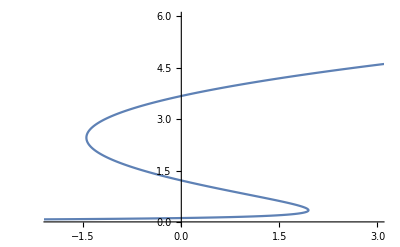

```mathematica
params={σ->0.2,δ->1,χ->0.2,α->1,μ->0.4,γ->0.1};
ListLinePlot[Table[{tisocline/.params,t},{t,-5,10,0.01}],PlotRange->{{-2,3},{0,6}}]
```

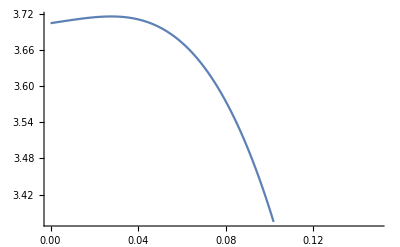

```mathematica
ListLinePlot[Table[{(p[T]/.sol3)[[1]],(t[T]/.sol3)[[1]]},{T,0,20,0.01}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p→0.,t→0.181875+0. ⅈ},{p→0.89525+0. ⅈ,t→0.261876+0. ⅈ},{p→0.675092+0. ⅈ,t→0.812271+0. ⅈ},{p→0.,t→1.11296+0. ⅈ},{p→-0.410341+0. ⅈ,t→3.52585+0. ⅈ},{p→0.,t→3.70516+0. ⅈ}}

Power::infy: Infinite expression 1/0. encountered.

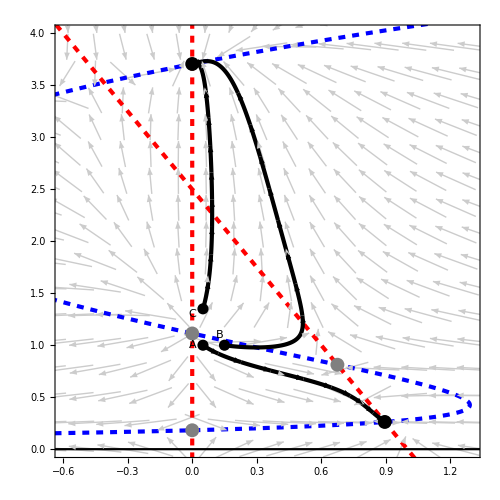

```mathematica
dp2=(1-p) p α-p t μ;
dt2=(γ+t (t-δ+p σ-t^2 χ))/δ;
pisocline=Solve[dp2==0,p][[2,1,2]];
tisocline=Solve[dt2==0,p][[1,1,2]];
params={σ->0.2,δ->1,χ->0.2,α->1,μ->0.4,γ->0.15};
sol1=NDSolve[{p'[T]==(dp2/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt2/.{p->p[T],t->t[T]}/.params),
p[0]==0.05,t[0]==1},{p,t},{T,0,50}];
sol2=NDSolve[{p'[T]==(dp2/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt2/.{p->p[T],t->t[T]}/.params),
p[0]==0.15,t[0]==1},{p,t},{T,0,50}];
sol3=NDSolve[{p'[T]==(dp2/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt2/.{p->p[T],t->t[T]}/.params),
p[0]==0.05,t[0]==1.35},{p,t},{T,0,50}];
equil=Solve[{dp2==0,dt2==0}/.params, {p,t}]
Show[VectorPlot[{dp2/.params,dt2/.params},{p,-2,2},{t,0,8},VectorScale->{0.028,0.6,None},VectorStyle->{GrayLevel[0.8]},VectorPoints->32],
ListLinePlot[Table[{tisocline/.params,t},{t,0,20,0.01}],PlotStyle->{Thickness[0.006],Dashed,Blue},PlotRange->All],
ListLinePlot[Table[{pisocline/.params,t},{t,-5,15,0.01}],PlotStyle->{Thickness[0.006],Dashed,Red}],
ListLinePlot[Table[{0,t},{t,-1,12,0.01}],PlotStyle->{Thickness[0.006],Dashed,Red}],
ListLinePlot[Table[{p,0},{p,-2,8,0.01}],PlotStyle->{Black}],
ListLinePlot[Table[{(p[T]/.sol1)[[1]],(t[T]/.sol1)[[1]]},{T,0,20,0.01}],PlotStyle->{Thickness[0.006],Black},MeshFunctions->{#2&},Mesh->8,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.03]}]/.Line->Arrow,
ListLinePlot[Table[{(p[T]/.sol2)[[1]],(t[T]/.sol2)[[1]]},{T,0,20,0.01}],PlotStyle->{Thickness[0.006],Black},MeshFunctions->{#2&},Mesh->8,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.03]}]/.Line->Arrow,
ListLinePlot[Table[{(p[T]/.sol3)[[1]],(t[T]/.sol3)[[1]]},{T,0,10,0.01}],PlotStyle->{Thickness[0.006],Black},MeshFunctions->{#2&},Mesh->8,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.03]}]/.Line->Arrow,
Graphics[{AbsolutePointSize[10],Gray,Point[{equil[[1,1,2]],equil[[1,2,2]]}]}],
Graphics[{AbsolutePointSize[10],Black,Point[{equil[[2,1,2]],equil[[2,2,2]]}]}],
Graphics[{AbsolutePointSize[10],Gray,Point[{equil[[3,1,2]],equil[[3,2,2]]}]}],
Graphics[{AbsolutePointSize[10],Black,Point[{equil[[6,1,2]],equil[[6,2,2]]}]}],
Graphics[{AbsolutePointSize[10],Gray,Point[{equil[[4,1,2]],equil[[4,2,2]]}]}],
Graphics[{AbsolutePointSize[8],Black,Point[{0.05,1}]}],
Graphics[{AbsolutePointSize[8],Black,Point[{0.15,1}]}],
Graphics[{AbsolutePointSize[8],Black,Point[{0.05,1.35}]}],
Graphics[Text[Style[A,Large],{0,1}]],
Graphics[Text[Style[B,Large],{0.13,1.1}]],
Graphics[Text[Style[C,Large],{0,1.3}]],
PlotRange->{{-0.6,1.3},{0,4}}]
```

Simplified version of above:

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p→0.,t→0.181875+0. ⅈ},{p→0.89525+0. ⅈ,t→0.261876+0. ⅈ},{p→0.675092+0. ⅈ,t→0.812271+0. ⅈ},{p→0.,t→1.11296+0. ⅈ},{p→-0.410341+0. ⅈ,t→3.52585+0. ⅈ},{p→0.,t→3.70516+0. ⅈ}}

Power::infy: Infinite expression 1/0. encountered.

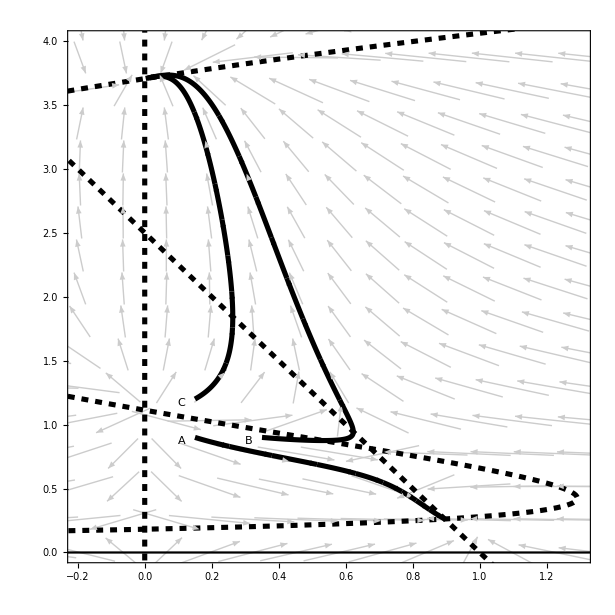

```mathematica
dp2=(1-p) p α-p t μ;
dt2=(γ+t (t-δ+p σ-t^2 χ))/δ;
pisocline=Solve[dp2==0,p][[2,1,2]];
tisocline=Solve[dt2==0,p][[1,1,2]];
params={σ->0.2,δ->1,χ->0.2,α->1,μ->0.4,γ->0.15};
sol1=NDSolve[{p'[T]==(dp2/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt2/.{p->p[T],t->t[T]}/.params),
p[0]==0.35,t[0]==0.9},{p,t},{T,0,50}];
sol2=NDSolve[{p'[T]==(dp2/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt2/.{p->p[T],t->t[T]}/.params),
p[0]==0.15,t[0]==0.9},{p,t},{T,0,50}];
sol3=NDSolve[{p'[T]==(dp2/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt2/.{p->p[T],t->t[T]}/.params),
p[0]==0.15,t[0]==1.2},{p,t},{T,0,50}];
equil=Solve[{dp2==0,dt2==0}/.params, {p,t}]
Show[VectorPlot[{dp2/.params,dt2/.params},{p,-2,2},{t,0,8},VectorScale->{0.028,0.6,None},VectorStyle->{GrayLevel[0.8]},VectorPoints->32],
ListLinePlot[Table[{tisocline/.params,t},{t,0,20,0.01}],PlotStyle->{Thickness[0.006],Dashed,Black},PlotRange->All],
ListLinePlot[Table[{pisocline/.params,t},{t,-2,15,0.01}],PlotStyle->{Thickness[0.006],Dashed,Black}],
ListLinePlot[Table[{0,t},{t,-1,12,0.01}],PlotStyle->{Thickness[0.006],Dashed,Black}],
ListLinePlot[Table[{p,0},{p,-2,8,0.01}],PlotStyle->{Black}],
ListLinePlot[Table[{(p[T]/.sol1)[[1]],(t[T]/.sol1)[[1]]},{T,0,20,0.01}],PlotStyle->{Thickness[0.006],Black},MeshFunctions->{#2&},Mesh->8,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.03]}]/.Line->Arrow,
ListLinePlot[Table[{(p[T]/.sol2)[[1]],(t[T]/.sol2)[[1]]},{T,0,20,0.01}],PlotStyle->{Thickness[0.006],Black},MeshFunctions->{#2&},Mesh->8,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.03]}]/.Line->Arrow,
ListLinePlot[Table[{(p[T]/.sol3)[[1]],(t[T]/.sol3)[[1]]},{T,0,10,0.01}],PlotStyle->{Thickness[0.006],Black},MeshFunctions->{#2&},Mesh->8,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.03]}]/.Line->Arrow,
Graphics[Text[Style[A,Large],{0.11,0.87}]],
Graphics[Text[Style[B,Large],{0.31,0.87}]],
Graphics[Text[Style[C,Large],{0.11,1.17}]],
PlotRange->{{-0.2,1.3},{0,4}}]
```

{0.341375,0.315569,0.33755,0.313293,0.287124,0.277982,0.297604,0.310465,0.348806,0.339479}

{0.948812,0.946466,0.735151,0.826376,0.726772,1.12211,0.756061,1.03003,1.19017,0.791873}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p→0.,t→0.181875+0. ⅈ},{p→0.89525+0. ⅈ,t→0.261876+0. ⅈ},{p→0.675092+0. ⅈ,t→0.812271+0. ⅈ},{p→0.,t→1.11296+0. ⅈ},{p→-0.410341+0. ⅈ,t→3.52585+0. ⅈ},{p→0.,t→3.70516+0. ⅈ}}

Power::infy: Infinite expression 1/0. encountered.

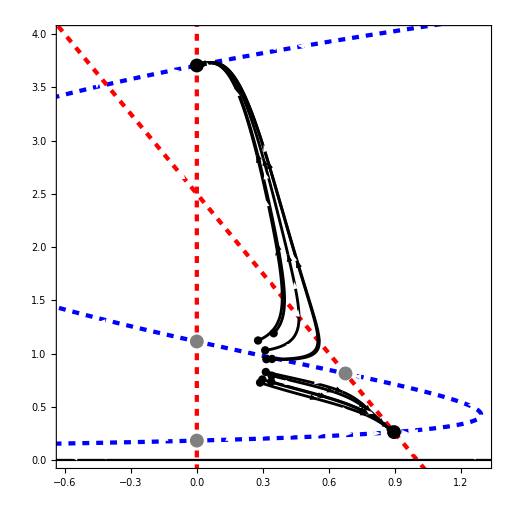

```mathematica
dp2=(1-p) p α-p t μ;
dt2=(γ+t (t-δ+p σ-t^2 χ))/δ;
pisocline=Solve[dp2==0,p][[2,1,2]];
tisocline=Solve[dt2==0,p][[1,1,2]];
params={σ->0.2,δ->1,χ->0.2,α->1,μ->0.4,γ->0.15};
initP=RandomReal[{0.25,0.35},10]
initT=RandomReal[{0.7,1.2},10]
sol1=NDSolve[{p'[T]==(dp2/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt2/.{p->p[T],t->t[T]}/.params),
p[0]==initP[[1]],t[0]==initT[[1]]},{p,t},{T,0,50}];
sol2=NDSolve[{p'[T]==(dp2/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt2/.{p->p[T],t->t[T]}/.params),
p[0]==initP[[2]],t[0]==initT[[2]]},{p,t},{T,0,50}];
sol3=NDSolve[{p'[T]==(dp2/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt2/.{p->p[T],t->t[T]}/.params),
p[0]==initP[[3]],t[0]==initT[[3]]},{p,t},{T,0,50}];
sol4=NDSolve[{p'[T]==(dp2/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt2/.{p->p[T],t->t[T]}/.params),
p[0]==initP[[4]],t[0]==initT[[4]]},{p,t},{T,0,50}];
sol5=NDSolve[{p'[T]==(dp2/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt2/.{p->p[T],t->t[T]}/.params),
p[0]==initP[[5]],t[0]==initT[[5]]},{p,t},{T,0,50}];
sol6=NDSolve[{p'[T]==(dp2/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt2/.{p->p[T],t->t[T]}/.params),
p[0]==initP[[6]],t[0]==initT[[6]]},{p,t},{T,0,50}];
sol7=NDSolve[{p'[T]==(dp2/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt2/.{p->p[T],t->t[T]}/.params),
p[0]==initP[[7]],t[0]==initT[[7]]},{p,t},{T,0,50}];
sol8=NDSolve[{p'[T]==(dp2/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt2/.{p->p[T],t->t[T]}/.params),
p[0]==initP[[8]],t[0]==initT[[8]]},{p,t},{T,0,50}];
sol9=NDSolve[{p'[T]==(dp2/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt2/.{p->p[T],t->t[T]}/.params),
p[0]==initP[[9]],t[0]==initT[[9]]},{p,t},{T,0,50}];
sol10=NDSolve[{p'[T]==(dp2/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt2/.{p->p[T],t->t[T]}/.params),
p[0]==initP[[10]],t[0]==initT[[10]]},{p,t},{T,0,50}];
equil=Solve[{dp2==0,dt2==0}/.params, {p,t}]
Show[
VectorPlot[{dp2/.params,dt2/.params},{p,-2,2},{t,0,8},VectorScale->{0.028,0.6,None},VectorStyle->{GrayLevel[1]},VectorPoints->32],
ListLinePlot[Table[{tisocline/.params,t},{t,0,20,0.01}],PlotStyle->{Thickness[0.006],Dashed,Blue},PlotRange->All],
ListLinePlot[Table[{pisocline/.params,t},{t,-5,15,0.01}],PlotStyle->{Thickness[0.006],Dashed,Red}],
ListLinePlot[Table[{0,t},{t,-1,12,0.01}],PlotStyle->{Thickness[0.006],Dashed,Red}],
ListLinePlot[Table[{p,0},{p,-2,8,0.01}],PlotStyle->{Black}],
ListLinePlot[Table[{(p[T]/.sol1)[[1]],(t[T]/.sol1)[[1]]},{T,0,20,0.01}],PlotStyle->{Thickness[0.004],Black},MeshFunctions->{#2&},Mesh->2,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.02]}]/.Line->Arrow,
ListLinePlot[Table[{(p[T]/.sol2)[[1]],(t[T]/.sol2)[[1]]},{T,0,20,0.01}],PlotStyle->{Thickness[0.004],Black},MeshFunctions->{#2&},Mesh->2,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.02]}]/.Line->Arrow,
ListLinePlot[Table[{(p[T]/.sol3)[[1]],(t[T]/.sol3)[[1]]},{T,0,10,0.01}],PlotStyle->{Thickness[0.004],Black},MeshFunctions->{#2&},Mesh->2,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.02]}]/.Line->Arrow,
ListLinePlot[Table[{(p[T]/.sol4)[[1]],(t[T]/.sol4)[[1]]},{T,0,20,0.01}],PlotStyle->{Thickness[0.004],Black},MeshFunctions->{#2&},Mesh->2,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.02]}]/.Line->Arrow,
ListLinePlot[Table[{(p[T]/.sol5)[[1]],(t[T]/.sol5)[[1]]},{T,0,20,0.01}],PlotStyle->{Thickness[0.004],Black},MeshFunctions->{#2&},Mesh->2,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.02]}]/.Line->Arrow,
ListLinePlot[Table[{(p[T]/.sol6)[[1]],(t[T]/.sol6)[[1]]},{T,0,10,0.01}],PlotStyle->{Thickness[0.004],Black},MeshFunctions->{#2&},Mesh->2,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.02]}]/.Line->Arrow,
ListLinePlot[Table[{(p[T]/.sol7)[[1]],(t[T]/.sol7)[[1]]},{T,0,20,0.01}],PlotStyle->{Thickness[0.004],Black},MeshFunctions->{#2&},Mesh->2,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.02]}]/.Line->Arrow,
ListLinePlot[Table[{(p[T]/.sol8)[[1]],(t[T]/.sol8)[[1]]},{T,0,20,0.01}],PlotStyle->{Thickness[0.004],Black},MeshFunctions->{#2&},Mesh->2,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.02]}]/.Line->Arrow,
ListLinePlot[Table[{(p[T]/.sol9)[[1]],(t[T]/.sol9)[[1]]},{T,0,10,0.01}],PlotStyle->{Thickness[0.004],Black},MeshFunctions->{#2&},Mesh->2,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.02]}]/.Line->Arrow,
ListLinePlot[Table[{(p[T]/.sol10)[[1]],(t[T]/.sol10)[[1]]},{T,0,10,0.01}],PlotStyle->{Thickness[0.004],Black},MeshFunctions->{#2&},Mesh->2,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.03]}]/.Line->Arrow,
Graphics[{AbsolutePointSize[10],Gray,Point[{equil[[1,1,2]],equil[[1,2,2]]}]}],
Graphics[{AbsolutePointSize[10],Black,Point[{equil[[2,1,2]],equil[[2,2,2]]}]}],
Graphics[{AbsolutePointSize[10],Gray,Point[{equil[[3,1,2]],equil[[3,2,2]]}]}],
Graphics[{AbsolutePointSize[10],Black,Point[{equil[[6,1,2]],equil[[6,2,2]]}]}],
Graphics[{AbsolutePointSize[10],Gray,Point[{equil[[4,1,2]],equil[[4,2,2]]}]}],
Graphics[{AbsolutePointSize[6],Black,Point[{initP[[1]],initT[[1]]}]}],
Graphics[{AbsolutePointSize[6],Black,Point[{initP[[2]],initT[[2]]}]}],
Graphics[{AbsolutePointSize[6],Black,Point[{initP[[3]],initT[[3]]}]}],
Graphics[{AbsolutePointSize[6],Black,Point[{initP[[4]],initT[[4]]}]}],
Graphics[{AbsolutePointSize[6],Black,Point[{initP[[5]],initT[[5]]}]}],
Graphics[{AbsolutePointSize[6],Black,Point[{initP[[6]],initT[[6]]}]}],
Graphics[{AbsolutePointSize[6],Black,Point[{initP[[7]],initT[[7]]}]}],
Graphics[{AbsolutePointSize[6],Black,Point[{initP[[8]],initT[[8]]}]}],
Graphics[{AbsolutePointSize[6],Black,Point[{initP[[9]],initT[[9]]}]}],
Graphics[{AbsolutePointSize[6],Black,Point[{initP[[10]],initT[[10]]}]}],
PlotRange->{{-0.6,1.3},{0,4}}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p→0.,t→10000.},{p→0.0964785,t→4.51761},{p→0.609383,t→1.95308}}

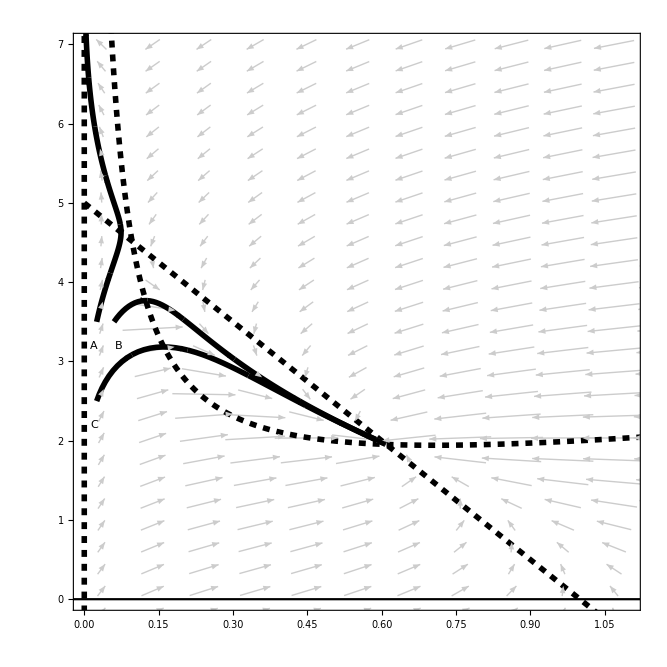

```mathematica
dt=γ+β p-ν t-α p/(1+p) t;
dp=λ p (1-p)-κ p t;
tisocline=Solve[dt==0,t][[1,1,2]]//Simplify;
pisocline=Solve[dp==0,t][[1,1,2]];
params={β->2,γ->1,κ->0.8,λ->4,α->3,ν->0.0001};
equil=Solve[{dp==0,dt==0}/.params,{p,t}]

sol1=NDSolve[{p'[T]==(dp/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt/.{p->p[T],t->t[T]}/.params),
p[0]==0.025,t[0]==3.5},{p,t},{T,0,50}];
sol2=NDSolve[{p'[T]==(dp/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt/.{p->p[T],t->t[T]}/.params),
p[0]==0.06,t[0]==3.5},{p,t},{T,0,50}];
sol3=NDSolve[{p'[T]==(dp/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt/.{p->p[T],t->t[T]}/.params),
p[0]==0.025,t[0]==2.5},{p,t},{T,0,50}];
Show[VectorPlot[{dp/.params,dt/.params},{p,-1,2},{t,-1,7},VectorScale->{0.015,0.5,None},VectorStyle->{GrayLevel[0.8]},VectorPoints->30],
ListLinePlot[Table[{p,tisocline/.params},{p,0,5,0.001}],PlotStyle->{Thickness[0.006],Dashed,Black},PlotRange->All],
ListLinePlot[Table[{p, pisocline/.params},{p,0,5,0.01}],PlotStyle->{Thickness[0.006],Dashed,Black}],
ListLinePlot[Table[{0,t},{t,-1,12,0.01}],PlotStyle->{Thickness[0.006],Dashed,Black}],
ListLinePlot[Table[{p,0},{p,-1,8,0.01}],PlotStyle->{Medium,Black}],
ListLinePlot[Table[{(p[T]/.sol1)[[1]],(t[T]/.sol1)[[1]]},{T,0,10,0.01}],PlotStyle->{Thickness[0.006],Black},MeshFunctions->{#2&},Mesh->8,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.03]}]/.Line->Arrow,
ListLinePlot[Table[{(p[T]/.sol2)[[1]],(t[T]/.sol2)[[1]]},{T,0,10,0.1}],PlotStyle->{Thickness[0.006],Black},MeshFunctions->{#3&},Mesh->8,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.03]}]/.Line->Arrow,
ListLinePlot[Table[{(p[T]/.sol3)[[1]],(t[T]/.sol3)[[1]]},{T,0,8,0.1}],PlotStyle->{Thickness[0.006],Black},MeshFunctions->{#3&},Mesh->8,MeshStyle->Opacity[0],MeshShading->{Arrowheads[0.03]}]/.Line->Arrow,
Graphics[Text[Style[A,Large],{0.02,3.2}]],
Graphics[Text[Style[B,Large],{0.07,3.2}]],
Graphics[Text[Style[C,Large],{0.02,2.2}]],
PlotRange->{{0,1.1},{0,7}}]
```

### Parasite-mediated feedback model

```mathematica
dt=γ+β p-ν t-α p/(1+p) t
dp=λ p-κ p t
```

-(p t α)/(1+p)+p β+γ-t ν

-p t κ+p λ

Here is proof of bistability for a particular set of parameter values.

```mathematica
params={β->1.5,γ->1,κ->0.9,λ->2,α->1.95,ν->0.25};
Solve[{dp==0,dt==0},{p,t}]/.params
Eigenvalues[D[{dp,dt},{{p,t}}]]/.Solve[{dp==0,dt==0},{p,t}]/.params
```

{{p→0,t→4.},{p→0.215098,t→2.22222},{p→1.37749,t→2.22222}}

{{-1.6,-0.25},{-0.902865,0.307674},{-0.689904-0.658202 ⅈ,-0.689904+0.658202 ⅈ}}

And here’s what the isoclines look like:

```mathematica
tisocline=Solve[dt==0,p][[1,1,2]]//Simplify
pisocline=Solve[dp==0,t][[1,1,2]]
```

-(-t α+β+γ-t ν+√(-4 β (γ-t ν)+(β+γ-t (α+ν))^2))/(2 β)

λ/κ

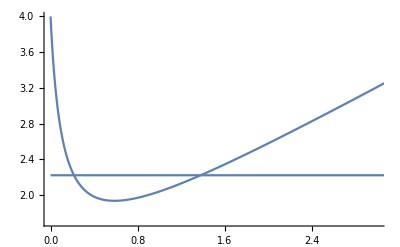

```mathematica
Show[ListLinePlot[Table[{p,((1+p) (p β+γ))/(p α+ν+p ν)/.params},{p,0,5,0.01}]],Plot[pisocline/.params,{t,0,5}],PlotRange->{{0,3},{1.7,4}}]
```

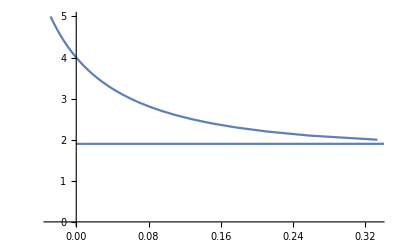

```mathematica
Show[ListLinePlot[Table[{tisocline/.params,t},{t,2,5,0.1}]],Plot[pisocline/.params,{t,0,5}]]
```

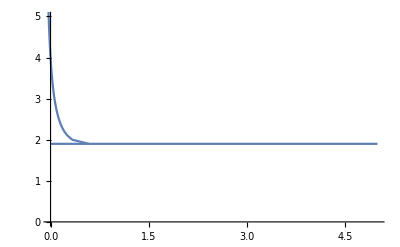

```mathematica
Show[ListLinePlot[Table[{tisocline/.params,t},{t,-5,15,0.1}]],Plot[pisocline/.params,{t,0,5}],PlotRange->{{0,5},{0,5}}]
```

Here’s a model with density-dependent parasite growth:

```mathematica
dt=γ+β p-ν t-α p/(1+p) t
dp=λ p (1-p)-κ p t
```

-(p t α)/(1+p)+p β+γ-t ν

-p t κ+(1-p) p λ

```mathematica
tisocline=Solve[dt==0,t][[1,1,2]]//Simplify
pisocline=Solve[dp==0,t][[1,1,2]]
```

(p (1+p) β)/(ν+p (α+ν))

-((-1+p) λ)/κ

Here is a case with a single stable equilibrium.

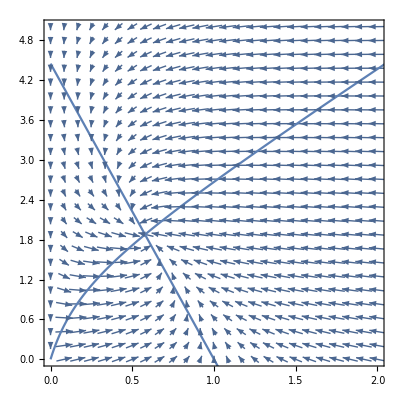

```mathematica
params={β->2,γ->1,κ->0.9,λ->4,α->1,ν->0.25};Show[VectorPlot[{dp/.params,dt/.params},{p,0,2},{t,0,5},VectorScale->{0.02,0.8,None},VectorPoints->25],
ListLinePlot[Table[{p,tisocline/.params},{p,0,5,0.01}]],
ListLinePlot[Table[{p, pisocline/.params},{p,0,5,0.01}]],PlotRange->{{0,2},{0,5}}]
```

```mathematica
(* There should be a single stable equilibrium if the value of the p isocline when p=0 is greater than the value of the t isocline when p=0; there is the possibility of bistability if the opposite is true *)
(* The value of the t isocline when p = 0 *)
tisocline/.p->0
(* The value of the p isocline when p = 0 *)
pisocline/.p->0
```

0

λ/κ

```mathematica
(* There can be two internal intersections if γ/ν > λ/κ *)
```

True

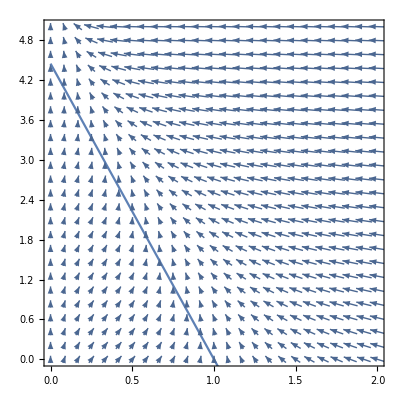

```mathematica
(* Here's a case where that doesn't happen, because everything is too big *)
params={β->2,γ->2,κ->0.9,λ->4,α->1,ν->0.25};
γ/ν > λ/κ/.params
Show[VectorPlot[{dp/.params,dt/.params},{p,0,2},{t,0,5},VectorScale->{0.02,0.8,None},VectorPoints->25],
ListLinePlot[Table[{p,tisocline/.params},{p,0,5,0.01}]],
ListLinePlot[Table[{p, pisocline/.params},{p,0,5,0.01}]],PlotRange->{{0,2},{0,5}}]
```

The more you increase the value of ν, the steeper the decline in the t isocline as p increases away from p = 0, and the lower the intersection with the t axis.

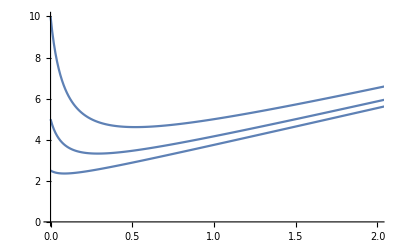

```mathematica
Show[
ListLinePlot[Table[{p,tisocline/.{β->2,γ->1,κ->0.9,λ->4,α->1,ν->0.1}},{p,0,5,0.01}]],
ListLinePlot[Table[{p,tisocline/.{β->2,γ->0.5,κ->0.9,λ->4,α->1,ν->0.1}},{p,0,5,0.01}]],
ListLinePlot[Table[{p,tisocline/.{β->2,γ->0.25,κ->0.9,λ->4,α->1,ν->0.1}},{p,0,5,0.01}]],
PlotRange->{{0,2},{0,10}}]
```

Here is a case with bistability.

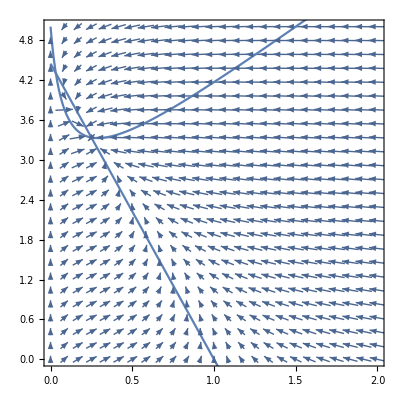

```mathematica
params={β->2,γ->0.5,κ->0.9,λ->4,α->1,ν->0.1};
Show[VectorPlot[{dp/.params,dt/.params},{p,0,2},{t,0,5},VectorScale->{0.02,0.8,None},VectorPoints->25],
ListLinePlot[Table[{p,tisocline/.params},{p,0,5,0.01}]],
ListLinePlot[Table[{p, pisocline/.params},{p,0,5,0.01}]],PlotRange->{{0,2},{0,5}}]
```

A little more analysis might be helpful here. We want the minimum of the t isocline to be somewhere between 0 and 1, and we want it to be as low as possible.

```mathematica
Simplify[Solve[Numerator[Simplify[D[tisocline,p]]]==0,p]]
```

{{p→-(β ν+√(α β (α γ+(-β+γ) ν)))/(β (α+ν))},{p→(-β ν+√(α β (α γ+(-β+γ) ν)))/(β (α+ν))}}

β > γ guarantees that the minimum is a real number. The larger α is (or the smaller ν is), the further that minimum is to the right.

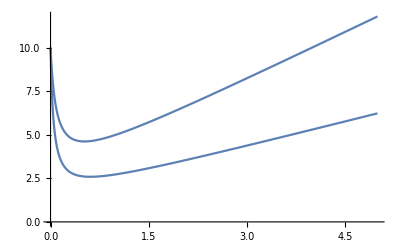

```mathematica
Show[ListLinePlot[Table[{p,tisocline/.{β->2,γ->1,κ->0.9,λ->4,α->1,ν->0.1}},{p,0,5,0.01}]],
ListLinePlot[Table[{p,tisocline/.{β->2,γ->1,κ->0.9,λ->4,α->2,ν->0.1}},{p,0,5,0.01}]]]
```

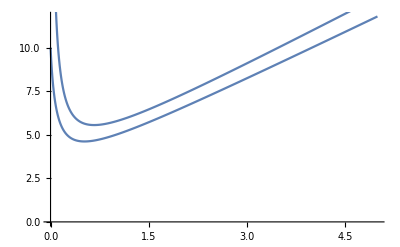

```mathematica
Show[ListLinePlot[Table[{p,tisocline/.{β->2,γ->1,κ->0.9,λ->4,α->1,ν->0.1}},{p,0,5,0.01}]],
ListLinePlot[Table[{p,tisocline/.{β->2,γ->1,κ->0.9,λ->4,α->1,ν->0.02}},{p,0,5,0.01}]]]
```

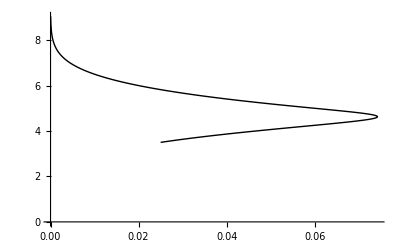

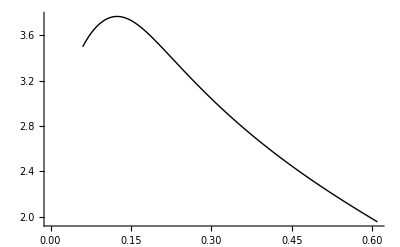

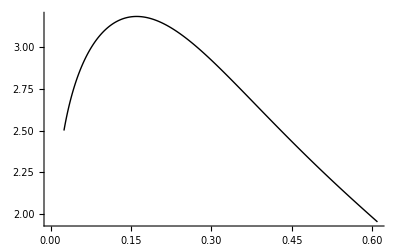

```mathematica
sol1=NDSolve[{p'[T]==(dp/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt/.{p->p[T],t->t[T]}/.params),
p[0]==0.025,t[0]==3.5},{p,t},{T,0,50}];
ListLinePlot[Table[{(p[T]/.sol1)[[1]],(t[T]/.sol1)[[1]]},{T,0,10,0.01}],PlotStyle->{Thick,Black}]
sol2=NDSolve[{p'[T]==(dp/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt/.{p->p[T],t->t[T]}/.params),
p[0]==0.06,t[0]==3.5},{p,t},{T,0,50}];
ListLinePlot[Table[{(p[T]/.sol2)[[1]],(t[T]/.sol2)[[1]]},{T,0,20,0.01}],PlotStyle->{Thick,Black}]
sol3=NDSolve[{p'[T]==(dp/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt/.{p->p[T],t->t[T]}/.params),
p[0]==0.025,t[0]==2.5},{p,t},{T,0,50}];
ListLinePlot[Table[{(p[T]/.sol3)[[1]],(t[T]/.sol3)[[1]]},{T,0,20,0.01}],PlotStyle->{Thick,Black}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p→0.,t→10000.},{p→0.0964785,t→4.51761},{p→0.609383,t→1.95308}}

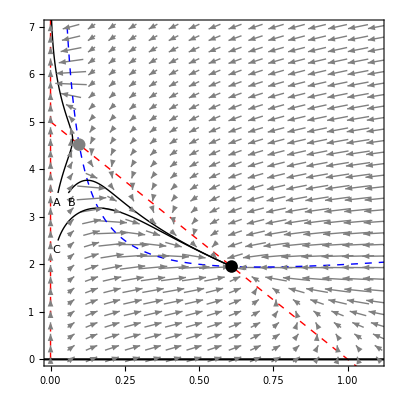

```mathematica
params={β->2,γ->1,κ->0.8,λ->4,α->3,ν->0.0001};
equil=Solve[{dp==0,dt==0}/.params,{p,t}]
Show[VectorPlot[{dp/.params,dt/.params},{p,0,2},{t,0,7},VectorScale->{0.015,0.5,None},VectorStyle->{GrayLevel[0.5]},VectorPoints->30],
ListLinePlot[Table[{p,tisocline/.params},{p,0,5,0.001}],PlotStyle->{Thick,Dashed,Blue},PlotRange->All],
ListLinePlot[Table[{p, pisocline/.params},{p,0,5,0.01}],PlotStyle->{Thick,Dashed,Red}],
ListLinePlot[Table[{0,t},{t,-1,12,0.01}],PlotStyle->{Thick,Dashed,Red}],ListLinePlot[Table[{p,0},{p,-1,8,0.01}],PlotStyle->{Medium,Black}],
Graphics[{AbsolutePointSize[9],Black,Point[{equil[[1,1,2]],equil[[1,2,2]]}]}],
Graphics[{AbsolutePointSize[9],Gray,Point[{equil[[2,1,2]],equil[[2,2,2]]}]}],
Graphics[{AbsolutePointSize[9],Black,Point[{equil[[3,1,2]],equil[[3,2,2]]}]}],
ListLinePlot[Table[{(p[T]/.sol1)[[1]],(t[T]/.sol1)[[1]]},{T,0,10,0.01}],PlotStyle->{Thick,Black}],
ListLinePlot[Table[{(p[T]/.sol2)[[1]],(t[T]/.sol2)[[1]]},{T,0,10,0.01}],PlotStyle->{Thick,Black}],
ListLinePlot[Table[{(p[T]/.sol3)[[1]],(t[T]/.sol3)[[1]]},{T,0,10,0.01}],PlotStyle->{Thick,Black}],
Graphics[Text[Style[A,Medium],{0.02,3.3}]],
Graphics[Text[Style[B,Medium],{0.07,3.3}]],
Graphics[Text[Style[C,Medium],{0.02,2.3}]],
PlotRange->{{0,1.1},{0,7}}]
```

-Graphics-

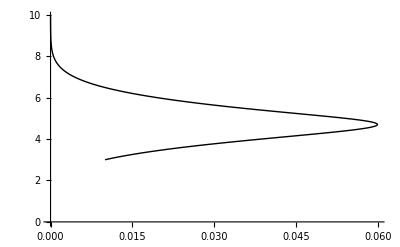

```mathematica
sol1=NDSolve[{p'[T]==(dp/.{p->p[T],t->t[T]}/.params),
t'[T]==(dt/.{p->p[T],t->t[T]}/.params),
p[0]==0.025,t[0]==3.5},{p,t},{T,0,50}];
ListLinePlot[Table[{(p[T]/.sol1)[[1]],(t[T]/.sol1)[[1]]},{T,0,10,0.01}],PlotStyle->{Thick,Black}]
```

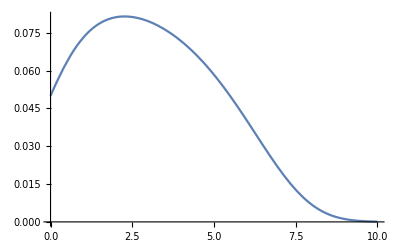

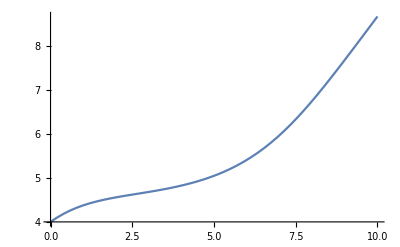

```mathematica
Plot[p[T]/.sol,{T,0,10}]
Plot[t[T]/.sol,{T,0,10}]
```

### Putting the models together

The two models are actually pretty different, so I need to figure out how to put them together coherently, such that I can smoothly adjust the strength of the immune-mediated versus parasite-mediated feedback processes.

Here are the two models together with parameter sets that produce bistability between an acute and a chronic equilibrium.

```mathematica
dt=γ+β p-ν t-α p/(1+p) t;
dp=λ p (1-p)-κ p t;
params={β->2,γ->0.5,κ->0.9,λ->4,α->1,ν->0.1};
equil=Solve[{dp==0,dt==0}/.params,{p,t}]
(* chronic equilibrium is stable *)
Eigenvalues[D[{dp,dt},{{p,t}}]]/.params/.equil[[1]]
(* acute equilibrium is stable *)
Eigenvalues[D[{dp,dt},{{p,t}}]]/.params/.equil[[3]]

dp2=(1-p) p α-p t μ;
dt2=(t (t-δ+p σ-t^2 χ))/δ;
params2={σ->0.2,δ->0.3,χ->0.1,α->0.5,μ->0.3};
equil2=Solve[{dp2==0,dt2==0}/.params2,{p,t}]
(* chronic equilibrium is stable *)
Eigenvalues[D[{dp2,dt2},{{p,t}}]]/.params2/.equil2[[1]]
(* acute equilibrium is stable *)
Eigenvalues[D[{dp2,dt2},{{p,t}}]]/.params2/.equil2[[6]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p→0.,t→5.},{p→0.0322581,t→4.30108},{p→0.25,t→3.33333}}

{-0.5,-0.1}

{-1.04051,-0.259488}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p→1.,t→0.},{p→0.,t→0.},{p→0.930914,t→0.115143},{p→0.,t→0.309584},{p→-4.21091,t→8.68486},{p→0.,t→9.69042}}

{-0.5,-0.333333}

{-30.3014,-2.40712}

You can see that these models are pretty different. In particular, in the parasite-mediated feedback model, the immune system has a baseline activation rate that is independent of parasites, and the parasite-dependent activation is actually independent of the state of the immune system, and dependent only on the number of parasites. In the immune-mediated model, the t = 0 equilibrium exists (which it doesn’t in the parasite-mediated model).

But recall that the immune-mediated feedback model, the immune cells are actually responding to cytokines, as well as parasites. 

Change the model up a bit, to account for the fact that parasites cause production of cytokines, and t cells respond to cytokines, not parasites.

So, in this new model, T cells are produced at a baseline rate γ; parasites cause the production of cytokines a per-parasite rate β; cytokines stimulate T cell activation at the per-capita rate σ; they also stimulate proliferation. 

Note that this model is kind of dimensionless without being properly derived, which is naughty. I’ll have to fix this later. But I’m time-pressed right now, so I’m trying to boogie along.

```mathematica
dp2=α p(1-p)-μ p t
ds2=β p+t-δ s
dt2=γ+σ s+s t-χ s t^2-t
```

(1-p) p α-p t μ

t+p β-s δ

-t+s t+γ+s σ-s t^2 χ

Here is the quasi-equilibrium cytokine level:

```mathematica
Solve[ds2==0,s]
```

{{s→(t+p β)/δ}}

```mathematica
dt2=FullSimplify[dt2/.{s->(t+p β)/δ}]
```

(t (t+p β)-t δ+γ δ+(t+p β) σ-t^2 (t+p β) χ)/δ

This is a super-interesting model because now parasites can increase the amount of cell death that happens through increasing activation - that’s pretty cool, and biologically reasonable!

Note that t = 0 is no longer a feasible equilibrium, though.

```mathematica
params2={σ->0.2,δ->0.3,χ->0.1,α->0.5,μ->0.3,γ->0.01,β->1};
equil2=Solve[{dp2==0,dt2==0}/.params2,{p,t}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p→2.07625+0. ⅈ,t→-1.79376+0. ⅈ},{p→1.17703+0. ⅈ,t→-0.295058+0. ⅈ},{p→0.,t→0.0503556-0.0222448 ⅈ},{p→0.,t→0.0503556+0.0222448 ⅈ},{p→-4.75329+0. ⅈ,t→9.58882+0. ⅈ},{p→0.,t→9.89929}}

The t isocline intersects the p axis at a negative t value - does that matter? I guess not.

```mathematica
(Solve[dt2==0,p])[[1,1,2]]/.t->0
```

-(γ δ)/(β σ)

```mathematica
Solve[Numerator[(Solve[dt2==0,p])[[1,1,2]]]==0,t]/.params2
```

{{t→0.0503556+0.0222448 ⅈ},{t→9.89929+2.22045×10^-16 ⅈ},{t→0.0503556-0.0222448 ⅈ}}

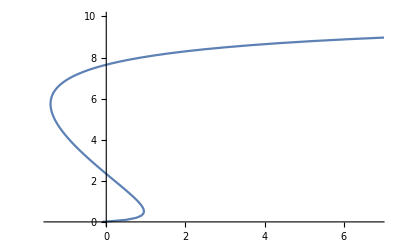

```mathematica
params2={σ->0.2,δ->2,χ->0.1,α->0.5,μ->0.3,γ->0.01,β->1};
ListLinePlot[Table[{(Solve[dt2==0,p]/.params2)[[1,1,2]],t},{t,0,10,0.1}]]
```

```mathematica
Solve[Denominator[Solve[dt2==0,p][[1,1,2]]]==0,t]
Solve[Denominator[Solve[dt2==0,p][[1,1,2]]]==0,t]/.{σ->0.2,δ->2,χ->0.1,α->0.5,μ->0.3,γ->0.01,β->1}
Solve[Denominator[Solve[dt2==0,p][[1,1,2]]]==0,t]/.{σ->0.2,δ->2,χ->1,α->0.5,μ->0.3,γ->0.01,β->1}
```

{{t→(1-√(1+4 σ χ))/(2 χ)},{t→(1+√(1+4 σ χ))/(2 χ)}}

{{t→-0.196152},{t→10.1962}}

{{t→-0.17082},{t→1.17082}}

```mathematica
params2={σ->0.2,δ->2,χ->0.1,α->0.5,μ->0.3,γ->0.01,β->1};
ListLinePlot[Table[{(Solve[dt2==0,p]/.params2)[[1,1,2]],t},{t,0,10,0.1}]]
```

-Graphics-

```mathematica
dt2/.params2/.p->0.25/.t->1
dt2/.params2/.p->2/.t->1
```

-0.3025

0.66

At issue, I think, is the fact that, as more interactions are added in, the immune model becomes increasingly unwieldy. However, I’m beginning to wonder if this model, with its inclusion of parasites affecting cytokine production affecting cytokine-induced cell death, is sufficiently complex to allow for both immune-mediated positive feedbacks and parasite-mediated positive feedbacks.

In particular, in this model, I can strengthen immune-mediated feedbacks by making T cell proliferation more sensitive:

```mathematica
dp2=α p(1-p)-μ p t;
dt2=(t (t+p β)-t δ+γ δ+(t+p β) σ-t^2 (t+p β) χ)/δ;
pisocline=Solve[dp2==0,t]⟦1,1,2⟧
tisocline=Solve[dt2==0,p][[1,1,2]]
```

-((-1+p) α)/μ

(t^2-t δ+γ δ+t σ-t^3 χ)/(β (-t-σ+t^2 χ))

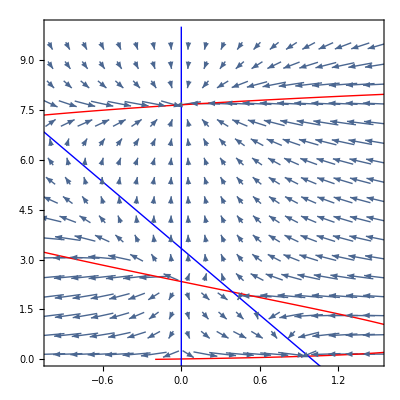

```mathematica
(* Here is the weak proliferation case *)
params2={σ->0.2,δ->2,χ->0.1,α->1,μ->0.3,γ->0.01,β->0.5};Show[VectorPlot[{dp2/.params2, dt2/.params2},{p,-1,1.5},{t,-1,10}, VectorScale->{0.02,0.4,None},VectorPoints->20],
ListLinePlot[Table[{tisocline/.params2,t},{t,0,10,0.01}],PlotStyle->{Thick,Red}],
ListLinePlot[Table[{p,pisocline/.params2},{p,-2,2,0.01}],PlotStyle->{Thick,Blue}],
ListLinePlot[Table[{0,t},{t,-10,10,0.01}], PlotStyle->{Thick,Blue}],PlotRange->{{-1,1.5},{0,10}}]
```

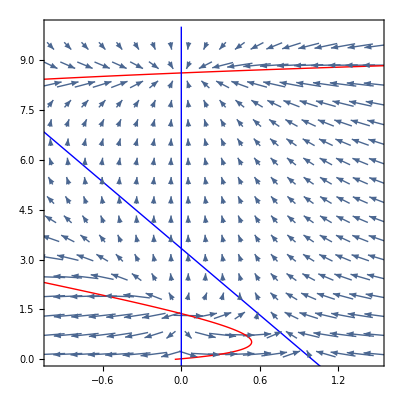

```mathematica
(* Here is the stronger proliferation case *)
(* Now there is only a single infection outcome - clearance *)
params2={σ->0.8,δ->2,χ->0.1,α->1,μ->0.3,γ->0.01,β->0.5};Show[VectorPlot[{dp2/.params2, dt2/.params2},{p,-1,1.5},{t,-1,10}, VectorScale->{0.02,0.4,None},VectorPoints->20],
ListLinePlot[Table[{tisocline/.params2,t},{t,0,10,0.01}],PlotStyle->{Thick,Red}],
ListLinePlot[Table[{p,pisocline/.params2},{p,-2,2,0.01}],PlotStyle->{Thick,Blue}],
ListLinePlot[Table[{0,t},{t,-10,10,0.01}], PlotStyle->{Thick,Blue}],PlotRange->{{-1,1.5},{0,10}}]
```

```mathematica
Solve[(tisocline/.params2)==0,t]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{t→0.0111804},{t→3.32774-0.922884 ⅈ},{t→3.32774+0.922884 ⅈ}}

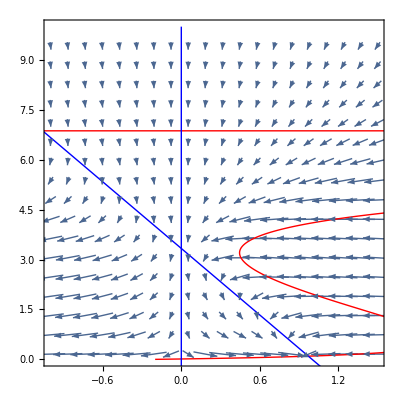

```mathematica
(* What happens if I make AICD more sensitive, essentially making the parasite better at indirect immunomodulation *)
(* Then the only equiliribum is the chronic infection equilibrium *)
(* Note that the top red line here is just showing the hyperbolic behavior of the model - it's not actually part of the isocline *)
params2={σ->0.2,δ->2,χ->0.15,α->1,μ->0.3,γ->0.01,β->0.5};Show[VectorPlot[{dp2/.params2, dt2/.params2},{p,-1,1.5},{t,-1,10}, VectorScale->{0.02,0.4,None},VectorPoints->20],
ListLinePlot[Table[{tisocline/.params2,t},{t,0,10,0.01}],PlotStyle->{Thick,Red}],
ListLinePlot[Table[{p,pisocline/.params2},{p,-2,2,0.01}],PlotStyle->{Thick,Blue}],
ListLinePlot[Table[{0,t},{t,-10,10,0.01}], PlotStyle->{Thick,Blue}],PlotRange->{{-1,1.5},{0,10}}]
```

This is all well and good, but I don’t see any feasible way to get the result that increasing dose goes from acute to chronic with this model.

What happens if you remove AICD (so you can replace it with manipulation). Can you still get bistability without it?

Looks like the answer is NO - you need the t isocline to cross at least 3 times, and you only get two here. There is some weird shit though - without AICD, the system runs away with itself - the parasite goes extinct but the immune system exhibits something akin to immunopathology

```mathematica
params2={σ->0.2,δ->2,χ->0,α->1,μ->0.3,γ->0.01,β->0.5};
Solve[(tisocline/.χ->0)==0,t]
Solve[(tisocline/.χ->0)==0,t]/.params2
```

{{t→1/2 (δ-σ-√(-4 γ δ+δ^2-2 δ σ+σ^2))},{t→1/2 (δ-σ+√(-4 γ δ+δ^2-2 δ σ+σ^2))}}

{{t→0.0111806},{t→1.78882}}

Notice that the parasite can end up cleared, but there is no equilibrium for the immune response after it is.

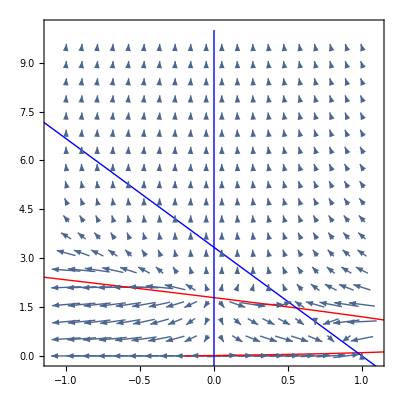

```mathematica
Show[VectorPlot[{dp2/.params2, dt2/.params2},{p,-1,1},{t,0,10}, VectorScale->{0.02,0.4,None},VectorPoints->20],
ListLinePlot[Table[{tisocline/.params2,t},{t,0,10,0.01}],PlotStyle->{Thick,Red}],
ListLinePlot[Table[{p,pisocline/.params2},{p,-2,2,0.01}],PlotStyle->{Thick,Blue}],
ListLinePlot[Table[{0,t},{t,-10,10,0.01}], PlotStyle->{Thick,Blue}]]
```

### Blah

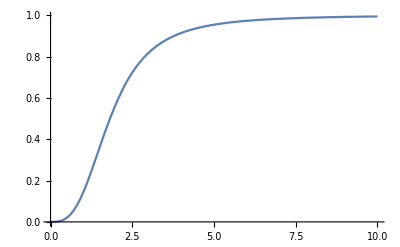

```mathematica
Plot[x^3/(6+x^3), {x,0,10},PlotRange->All]
```

```mathematica
di=a+b p^3/(h+p^3)-m i
dp=e p-d i p-u p
```

a-i m+(b p^3)/(h+p^3)

e p-d i p-p u

```mathematica
equil=Solve[{di==0,dp==0},{i,p}]//Simplify
```

{{i→a/m,p→0},{i→(e-u)/d,p→(-h (a d-e m+m u))^(1/3)/(a d+b d-e m+m u)^(1/3)},{i→(e-u)/d,p→-((-1)^(1/3) (-h (a d+m (-e+u)))^(1/3))/(a d+b d+m (-e+u))^(1/3)},{i→(e-u)/d,p→((-1)^(2/3) (-h (a d+m (-e+u)))^(1/3))/(a d+b d+m (-e+u))^(1/3)}}

To get a positive parasite equilibrium, a d-e m+m u<0 and a d+b d- e m+m u>0

```mathematica
params={a->0.1,b->5,m->0.1,e->2,d->0.2,u->0.1,h->10};
a d-e m+m u/.params
a d+b d-e m+m u/.params
a d-e m+m^2+√((a d-m (e+m-u))^2)+m u/.params
a d-e m+m^2-√((a d-m (e+m-u))^2)+m u/.params
equil/.params
```

-0.17

0.83

0.02

-0.34

{{i→1.,p→0},{i→9.5,p→1.26996},{i→9.5,p→-0.63498-1.09982 ⅈ},{i→9.5,p→-0.63498+1.09982 ⅈ}}

```mathematica
Collect[Expand[(gH H1-c H1-d1 H1+c p (H2+H3))+(gH H2-c H2-d2 H2+c p (H1+H3))+(gH H3-c H3-d3 H3+c p (H1+H2))],{gH,c}]/.p->0.5
```

0.-d1 H1-d2 H2-d3 H3+gH (H1+H2+H3)

```mathematica
evals/.equil[[1]]/.params
```

{-0.1,1.7}

```mathematica
evals=Eigenvalues[D[{di,dp},{{i,p}}]];
Assuming[a>0&&d>0&&e>0&&h>0&&m>0,Simplify[evals/.p->0/.i->a/m]]
Expand[(a d-m (e+m-u))]
```

{-(a d-e m+m^2+√((a d-m (e+m-u))^2)+m u)/(2 m),-(a d-e m+m^2-√((a d-m (e+m-u))^2)+m u)/(2 m)}

a d-e m-m^2+m u

```mathematica
dHdT=r H (1-H/K)-a H P
dPdT=e a H P-m P
```

-a H P+H (1-H/K) r

a e H P-m P

```mathematica
Simplify[Simplify[(dHdT/.{H->h hhat,P->p phat}) that/hhat]/.that->1/r/.hhat->K/.phat->r/a]
Simplify[(dPdT/.{H->h hhat,P->p phat}) that/phat]/.that->1/r/.hhat->K
```

-h (-1+h+p)

((a e h K-m) p)/r

```mathematica
dh=h(1-h)-h p
dp=α h p-μ p
```

(1-h) h-h p

h p α-p μ

```mathematica
evals=Simplify[Eigenvalues[D[{dh,dp},{{h,p}}]]]
```

{1/2 (1-p+h (-2+α)-μ-√(h^2 (2+α)^2+(1-p+μ)^2-2 h (p (-2+α)+(2+α) (1+μ)))),1/2 (1-p+h (-2+α)-μ+√(h^2 (2+α)^2+(1-p+μ)^2-2 h (p (-2+α)+(2+α) (1+μ))))}

```mathematica
equil=Solve[{dh==0,dp==0},{h,p}]
```

{{h→1,p→0},{h→μ/α,p→-(-α+μ)/α},{h→0,p→0}}

```mathematica
Assuming[α>0,FullSimplify[evals/.{h->μ/α,p->-(-α+μ)/α}]]
```

{-(μ+√(μ (μ+4 α (-α+μ))))/(2 α),(-μ+√(μ (μ+4 α (-α+μ))))/(2 α)}

If μ > α, then there is no tendency to oscillate (node, rather than focus), but not stable. So we require α > μ, but the closer α and μ are, the smaller that inherit tendency to oscillate will be. That’s the key. And α and μ are composite parameters: α = e a K/r and μ = m/r. So α being close to μ requires that e a K is only slightly bigger than m.

{-(a d-e m+m^2+√((a d-m (e+m-u))^2)+m u)/(2 m),-(a d-e m+m^2-√((a d-m (e+m-u))^2)+m u)/(2 m)}

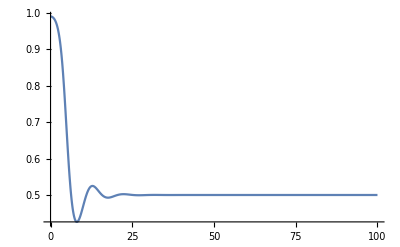

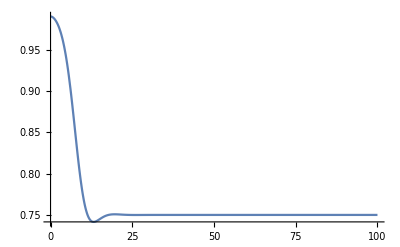

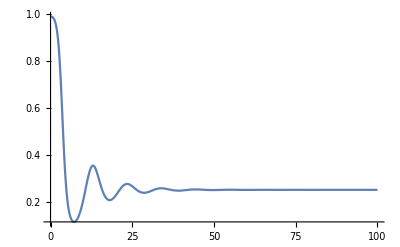

```mathematica
out1=NDSolve[{h'[t]==h[t](1-h[t])-h[t] p[t],p'[t]==α h[t] p[t]-μ p[t],h[0]==0.99,p[0]==0.01}/.{α->2,μ->1},{h,p},{t,0,100}];
Plot[h[t]/.out1,{t,0,100},PlotRange->All]
out1=NDSolve[{h'[t]==h[t](1-h[t])-h[t] p[t],p'[t]==α h[t] p[t]-μ p[t],h[0]==0.99,p[0]==0.01}/.{α->2,μ->1.5},{h,p},{t,0,100}];
Plot[h[t]/.out1,{t,0,100},PlotRange->All]
out1=NDSolve[{h'[t]==h[t](1-h[t])-h[t] p[t],p'[t]==α h[t] p[t]-μ p[t],h[0]==0.99,p[0]==0.01}/.{α->2,μ->0.5},{h,p},{t,0,100}];
Plot[h[t]/.out1,{t,0,100},PlotRange->All]
```